## Legend

Physics comments

Mathematica implementation comments/documentation

Miscellaneous comments

## Search Method + Search Algorithm

```mathematica
Import["/Users/sheridan/Academic/model_building/model_algebra.wl"]
```

```mathematica
Import["LieART`"]
```

LieART 2.0.2

last revised 21 August 2020

We define G as given in Eq. 5

```mathematica
G=SortBy[Select[Flatten[Table[{i,j,k},{i,2,9},{j,i,9},{k,j,9}],2],(#[[1]])^2+(#[[2]])^2+(#[[3]])^2-3<=78&&#[[3]]>=3&&#[[2]]>=2&],(#[[1]])^2+(#[[2]])^2+(#[[3]])^2-3&];
```

Compare the following with the text around Eq. 5

```mathematica
Print["|G| = ",Length@G]
Print["Minimal element = ",G[[1]]]
Print["Maximal element = ",G[[-1]]]
```

|G| = 39

Minimal element = {2,2,3}

Maximal element = {4,4,7}

Now we work toward exhibiting by generating all NABs induced by G and seeing which ones give rise to actual models

```mathematica
AllNABs=Flatten[DeleteCases[Select[#,#[[1]]>=3&&#[[2]]>=2&]&/@Permutations/@G,{}],1];
```

We can immediately eliminate NABs  merely based on their associated bifundamental representations  failing to decompose to a representation  of  which contains all of the necessary  SM representation terms (i.e., )

First, though, we implement this nice wrapper for Map (or /@) which gives us a basic progress bar (taken from here). Using Timing gives us a printout of runtime duration in seconds.

```mathematica
MapMonitored[f_,args_List]:=Module[{x=0},Monitor[MapIndexed[(x=#2[[1]];f[#1])&,args],ProgressIndicator[x/Length[args]]]]
```

Next we employ EmbedSMQ from model_algebra.wl, which returns a Boolean depending upon whether or not a given representation of contains the SM representation terms. From here, we keep only the NABs for which the associated decomposed representation  yields True from EmbedSMQ.

```mathematica
Timing[
AllNABsWithSMReps=MapMonitored[EmbedSMQ@BreakSUNGroupPair[#,{3,2,1},Bifundamental[#]]&,AllNABs];
][[1]]
```

18410.9

Note: above time is in units of seconds, and 18000 s = 5 hrs

```mathematica
AllNABsWithSMReps1=Select[MapThread[{#1,#2}&,{AllNABs,AllNABsWithSMReps}],#[[2]]&][[All,1]];
```

The groups which survive, forming , are as follows.

```mathematica
Gprime=DeleteDuplicates[Sort/@AllNABsWithSMReps1]
```

(3 | 3 | 4
3 | 4 | 4
3 | 3 | 5
3 | 4 | 5
4 | 4 | 5
3 | 5 | 5
3 | 4 | 6
4 | 5 | 5
3 | 3 | 7
3 | 5 | 6
3 | 4 | 7
4 | 5 | 6
4 | 4 | 7)

Compare the cardinality of computed below with the value stated after Eq. 8 in the text

```mathematica
Length@DeleteDuplicates[Sort/@AllNABsWithSMReps1]
```

13

Moreover, as claimed directly before Eq. 8, all NABs arising from the groups in satisfy the requirement of containing all  SM representation terms

```mathematica
Print["Number of NABs arising from  = "<>ToString@Length@AllNABsWithSMReps1]
Print["Number of NABs with necessary  SM representation terms = "<>ToString@Length@Flatten[DeleteCases[Select[#,#[[1]]>=3&&#[[2]]>=2&]&/@Permutations/@Gprime,{}],1]]
```

Number of NABs arising from  = 54

Number of NABs with necessary  SM representation terms = 54

Having found all NABs which contain the right  representations, plenty of NABs remain which yield no models. Thus, on our constrained list of NABs, we apply our primary workflow and determine which NABs produce models.

* COMMENT ON EMBEDSM *

```mathematica
data=MapMonitored[{#,EmbedSM[BreakSUNGroupPair[#,{3,2,1},Bifundamental[#]]]}&,AllNABsWithSMReps1];
```

## Results

We now print out a generalization of Table I in the text.

```mathematica
heads={"NAB ()", "Run Time", "","", "", "","", "", ""};
display={
#[[1]],
#[[2]]["duration"],
#[[2]]["numPossibleEmbed"],
#[[2]]["numUniqueSuccessEmbed"],
#[[2]]["numNoMCF"],
Length@#[[2]]["models"],
Length@DeleteDuplicates@#[[2]]["embedInfo"][[All,-2]],
Length@#[[2]]["uniqueContentModels"],
Length@Select[#[[2]]["uniqueContentModels"],Length@#[[2]]==0&]
}&/@data;
MatrixForm[display,TableHeadings->{None,heads}]
```

(NAB () | Run Time |  |  |  |  |  |  | 
{3,3,4} | 0.671384 s | 576 | 108 | 0 | 0 | 0 | 0 | 0
{3,4,3} | 0.343628 s | 540 | 48 | 0 | 0 | 0 | 0 | 0
{4,3,3} | 0.701576 s | 1008 | 84 | 84 | 48 | 9 | 2 | 1
{3,4,4} | 7.91174 s | 2688 | 696 | 444 | 252 | 24 | 1 | 0
{4,3,4} | 20.1216 s | 4320 | 1176 | 0 | 0 | 0 | 0 | 0
{4,4,3} | 14.0065 s | 2640 | 756 | 0 | 0 | 0 | 0 | 0
{3,3,5} | 6.75633 s | 2000 | 740 | 0 | 0 | 0 | 0 | 0
{3,5,3} | 8.1131 s | 1296 | 720 | 0 | 0 | 0 | 0 | 0
{5,3,3} | 14.4485 s | 3300 | 1086 | 1086 | 516 | 57 | 7 | 1
{3,4,5} | 1.58446 min | 9000 | 5200 | 0 | 0 | 0 | 0 | 0
{3,5,4} | 1.29839 min | 6336 | 3996 | 0 | 0 | 0 | 0 | 0
{4,3,5} | 2.99842 min | 13200 | 7040 | 0 | 0 | 0 | 0 | 0
{4,5,3} | 1.22026 min | 5040 | 2568 | 0 | 0 | 0 | 0 | 0
{5,3,4} | 4.51372 min | 13104 | 9228 | 0 | 0 | 0 | 0 | 0
{5,4,3} | 2.55313 min | 7200 | 4800 | 0 | 0 | 0 | 0 | 0
{4,4,5} | 15.2921 min | 32640 | 24600 | 0 | 0 | 0 | 0 | 0
{4,5,4} | 9.54054 min | 20520 | 14808 | 0 | 0 | 0 | 0 | 0
{5,4,4} | 15.49 min | 27360 | 20880 | 9148 | 5124 | 440 | 17 | 0
{3,5,5} | 7.06646 min | 21000 | 16020 | 1280 | 1074 | 120 | 3 | 0
{5,3,5} | 18.9061 min | 38080 | 29260 | 0 | 0 | 0 | 0 | 0
{5,5,3} | 6.5195 min | 12600 | 9042 | 0 | 0 | 0 | 0 | 0
{3,4,6} | 6.84177 min | 23760 | 16380 | 0 | 0 | 0 | 0 | 0
{3,6,4} | 3.45685 min | 11520 | 7632 | 0 | 0 | 0 | 0 | 0
{4,3,6} | 11.28 min | 32760 | 20520 | 2496 | 2304 | 67 | 2 | 0
{4,6,3} | 2.79883 min | 8208 | 4572 | 252 | 252 | 48 | 1 | 1
{6,3,4} | 15.3487 min | 28728 | 22512 | 0 | 0 | 0 | 0 | 0
{6,4,3} | 8.38923 min | 15120 | 11388 | 0 | 0 | 0 | 0 | 0
{4,5,5} | 46.3878 min | 60720 | 48400 | 4910 | 4360 | 353 | 13 | 0
{5,4,5} | 1.13992 h | 77280 | 62720 | 0 | 0 | 0 | 0 | 0
{5,5,4} | 41.2022 min | 46800 | 36900 | 0 | 0 | 0 | 0 | 0
{3,3,7} | 1.90983 min | 12348 | 6762 | 0 | 0 | 0 | 0 | 0
{3,7,3} | 51.577 s | 3780 | 2280 | 0 | 0 | 0 | 0 | 0
{7,3,3} | 4.63232 min | 14364 | 9870 | 9870 | 4920 | 537 | 55 | 5
{3,5,6} | 28.4108 min | 55080 | 44370 | 0 | 0 | 0 | 0 | 0
{3,6,5} | 19.2184 min | 38000 | 29360 | 0 | 0 | 0 | 0 | 0
{5,3,6} | 1.34518 h | 91200 | 74370 | 5024 | 3264 | 93 | 4 | 0
{5,6,3} | 28.8361 min | 19500 | 14352 | 468 | 336 | 60 | 1 | 1
{6,3,5} | 2.95792 h | 80960 | 66680 | 0 | 0 | 0 | 0 | 0
{6,5,3} | 1.06424 h | 25272 | 19620 | 0 | 0 | 0 | 0 | 0
{3,4,7} | 22.6769 min | 53508 | 39984 | 0 | 0 | 0 | 0 | 0
{3,7,4} | 7.59985 min | 18240 | 12420 | 0 | 0 | 0 | 0 | 0
{4,3,7} | 36.6461 min | 70560 | 48888 | 0 | 0 | 0 | 0 | 0
{4,7,3} | 6.17339 min | 12144 | 7152 | 0 | 0 | 0 | 0 | 0
{7,3,4} | 41.6899 min | 52992 | 43188 | 0 | 0 | 0 | 0 | 0
{7,4,3} | 21.7678 min | 27300 | 21624 | 0 | 0 | 0 | 0 | 0
{4,5,6} | 2.6775 h | 147420 | 122340 | 0 | 0 | 0 | 0 | 0
{4,6,5} | 9.27199 h | 97440 | 78400 | 0 | 0 | 0 | 0 | 0
{5,4,6} | 7.3454 h | 181440 | 152880 | 0 | 0 | 0 | 0 | 0
{5,6,4} | 6.24865 h | 71424 | 56904 | 0 | 0 | 0 | 0 | 0
{6,4,5} | 3.2632 h | 148800 | 124640 | 0 | 0 | 0 | 0 | 0
{6,5,4} | 1.92717 h | 88704 | 72504 | 0 | 0 | 0 | 0 | 0
{4,4,7} | 2.76477 h | 170016 | 140952 | 0 | 0 | 0 | 0 | 0
{4,7,4} | 42.1038 min | 48720 | 36456 | 0 | 0 | 0 | 0 | 0
{7,4,4} | 2.18734 h | 95232 | 78696 | 35522 | 13940 | 1008 | 45 | 0)

Total runtime:

```mathematica
Total@display[[All,2]]
```

181082. s

Note: 180000 s = 50 hrs

The final 6 columns of the above table coincide with the final 6 of Table I. As you can see, we in Table 1 we omit all NABs which yield no (possibly) phenomenologically viable models (i.e., NABs  which yield ). For your convenience, then, we now restate the above table with such rows removed.

```mathematica
MatrixForm[Select[display,#[[6]]>0&],TableHeadings->{None,heads}]
```

(NAB () | Run Time |  |  |  |  |  |  | 
{4,3,3} | 0.701576 s | 1008 | 84 | 84 | 48 | 9 | 2 | 1
{3,4,4} | 7.91174 s | 2688 | 696 | 444 | 252 | 24 | 1 | 0
{5,3,3} | 14.4485 s | 3300 | 1086 | 1086 | 516 | 57 | 7 | 1
{5,4,4} | 15.49 min | 27360 | 20880 | 9148 | 5124 | 440 | 17 | 0
{3,5,5} | 7.06646 min | 21000 | 16020 | 1280 | 1074 | 120 | 3 | 0
{4,3,6} | 11.28 min | 32760 | 20520 | 2496 | 2304 | 67 | 2 | 0
{4,6,3} | 2.79883 min | 8208 | 4572 | 252 | 252 | 48 | 1 | 1
{4,5,5} | 46.3878 min | 60720 | 48400 | 4910 | 4360 | 353 | 13 | 0
{7,3,3} | 4.63232 min | 14364 | 9870 | 9870 | 4920 | 537 | 55 | 5
{5,3,6} | 1.34518 h | 91200 | 74370 | 5024 | 3264 | 93 | 4 | 0
{5,6,3} | 28.8361 min | 19500 | 14352 | 468 | 336 | 60 | 1 | 1
{7,4,4} | 2.18734 h | 95232 | 78696 | 35522 | 13940 | 1008 | 45 | 0)

We also provide some additional information: namely, run time and “” is the number of possible choices of the integer w as described in the “Abelian Breaking Algorithm” section (in essence, the number of different instances of Eq. 12 which we tried to solve; the next column, , is then the number of those linear equations which yielded solutions).

We can verify Eq. 13 as follows.

```mathematica
Do[Print[""<>heads[[i]]<>" = "<>ToString@Total@display[[All,i]]],{i,4,9}]
```

= 1688572

= 70584

= 36390

= 2816

= 151

= 9

We can also verify the comment near the bottom of pg. 10 that ~80% of instances of Eq. 12 were solvable.

```mathematica
N@(Total@display[[All,4]]/Total@display[[All,3]])
```

0.784001

## Example Models

We now exhibit the example models discussed in the paper

```mathematica
goodData=Select[data,Length@#[[2]]["models"]>0&];
```

We define ℳ as given at the bottom of pg. 11

```mathematica
M=Flatten[Function[{group,gatheredModels},{group,#}&/@gatheredModels][#[[1]],#[[2]]["gatheredModels"]]&/@goodData,1];
M={#[[1]],#[[2,1,1]],#[[2,1,2]],#[[2,1,3]],Flatten[#,1]&/@#[[2,2]]}&/@M;
```

Now, we also define the equivalence classes of models by BSM chiral particle content as described at the top of pg. 17

```mathematica
chiralEquivClass=SortBy[GatherBy[M,#[[3]]&],NumParticles[#[[1,3]],1,2]&];
```

Indeed, we verify the number of equivalence classes we give on that same page

```mathematica
Length@chiralEquivClass
```

123

```mathematica
modelInfo={#[[1,3]], {#[[1]],#[[4]],Length@DeleteDuplicates[#[[5,All,{-2,-1}]]],Reverse/@DeleteDuplicates[#[[5,All,-2]]]}&/@#}&/@chiralEquivClass;
modelInfoDisplay={#[[1]],NumParticles[#[[1]],1,2],Length@#[[2]],Transpose@#[[2]]}&/@modelInfo;
```

Finally, we verify the number of those equivalence classes with ≤ 30 chiral BSM particles also stated on pg. 17

```mathematica
Length@Select[modelInfoDisplay,NumParticles[#[[1]],1,2]<=30&]
```

13

### Vector-Like Extensions

#### Setup

For clarity and convenience, we first present all of the strictly vector-like extensions we encounter in Small Bifundamental Theories. Columns feature the NAB in the first row and the BSM particle content in the second row (# of terms,  irrep, hypercharge).

```mathematica
VLs=modelInfoDisplay[[1,4]];
```

```mathematica
VLs[[1;;2]]
```

({4,3,3} | {5,3,3} | {4,6,3} | {7,3,3} | {7,3,3} | {7,3,3} | {7,3,3} | {7,3,3} | {5,6,3}
(3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
7 | (1,1) | 1/2
7 | (1,1) | -1/2
4 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
5 | (1,2) | 1/2
5 | (1,2) | -1/2
8 | (1,2) | 0
11 | (1,1) | 1/2
11 | (1,1) | -1/2
11 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
7 | (1,1) | 1
7 | (1,1) | -1
18 | (1,1) | 1/2
18 | (1,1) | -1/2
22 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
16 | (1,2) | 0
19 | (1,1) | 1/2
19 | (1,1) | -1/2
25 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
10 | (1,2) | 1/2
10 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 1
3 | (1,1) | -1
19 | (1,1) | 1/2
19 | (1,1) | -1/2
19 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 1
3 | (1,2) | -1
7 | (1,2) | 1/2
7 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 3/2
3 | (1,1) | -3/2
6 | (1,1) | 1
6 | (1,1) | -1
16 | (1,1) | 1/2
16 | (1,1) | -1/2
13 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 3/2
3 | (1,2) | -3/2
7 | (1,2) | 1/2
7 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 2
3 | (1,1) | -2
6 | (1,1) | 3/2
6 | (1,1) | -3/2
3 | (1,1) | 1
3 | (1,1) | -1
13 | (1,1) | 1/2
13 | (1,1) | -1/2
13 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
10 | (1,2) | 0
3 | (1,1) | 3/5
3 | (1,1) | -3/5
13 | (1,1) | 1/2
13 | (1,1) | -1/2
3 | (1,1) | 2/5
3 | (1,1) | -2/5
6 | (1,1) | 1/10
6 | (1,1) | -1/10
13 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
5 | (1,2) | 1/2
5 | (1,2) | -1/2
8 | (1,2) | 0
8 | (1,1) | 1
8 | (1,1) | -1
30 | (1,1) | 1/2
30 | (1,1) | -1/2
38 | (1,1) | 0))

However, our paper seeks to conjecture and characterize the existence of infinite classes of vector-like extensions: to extrapolate (i.e., to have at least two instances of models for each family we encounter), we need to apply EmbedSM to a few more gauge groups (i.e., ones which are BIGGER than SBTs). Namely,  (with NABs coinciding with the order given for the  factors). Specifically, N33 cases 2-5 require the NAB , and N63 case 2 requires the NAB . Additionally, we discover a new N63 class starting at , compelling us to explore  to see how that class extrapolates.

```mathematica
extrapolateData=MapMonitored[{#,EmbedSM[BreakSUNGroupPair[#,{3,2,1},Bifundamental[#]]]}&,{{8,3,3},{7,6,3},{8,6,3}}];
```

```mathematica
Total@(#[[2]]["duration"]&/@extrapolateData)
```

526.391 min

Note: 540 min = 9 hrs

```mathematica
extrapolateM=Flatten[Function[{group,gatheredModels},{group,#}&/@gatheredModels][#[[1]],#[[2]]["gatheredModels"]]&/@extrapolateData,1];
extrapolateM={#[[1]],#[[2,1,1]],#[[2,1,2]],#[[2,1,3]],Flatten[#,1]&/@#[[2,2]]}&/@extrapolateM;
extrapolateChiralEquivClass=SortBy[GatherBy[extrapolateM,#[[3]]&],NumParticles[#[[1,3]],1,2]&];
extrapolateModelInfo={#[[1,3]], {#[[1]],#[[4]],Length@DeleteDuplicates[#[[5,All,{-2,-1}]]],Reverse/@DeleteDuplicates[#[[5,All,-2]]]}&/@#}&/@extrapolateChiralEquivClass;
extrapolateModelInfoDisplay={#[[1]],NumParticles[#[[1]],1,2],Length@#[[2]],Transpose@#[[2]]}&/@extrapolateModelInfo;
```

```mathematica
extrapolateVLs=extrapolateModelInfoDisplay[[1,4]];
```

```mathematica
VLsWithExtra=Transpose@Join[Transpose@VLs,Transpose@extrapolateVLs];
```

```mathematica
FitCoefs[table_,index_]:=MapThread[{#1,#2}&,{table[[2,1,All,{2,3}]],LinearModelFit[MapThread[{#1,#2}&,{table[[1,All,index]],table[[2,All,#,1]]}],n,n]&/@Range[Length@table[[2,1]]]}]
```

In the subsubsections which follow, we do the same thing for each of the classes of vector-like extensions. Namely, we show the particular instances of the classes that we encountered, we provide linear fits for the coefficients for each of the irrep terms as a function of the varying  parameter, and provide a set of hypercharges (one for each class instance) which exhibits the conjectured trend for a generic hypercharge operator in general.

#### N33 Case 1

```mathematica
VLsN33Case1=VLsWithExtra[[1;;2,{1,2,4,10}]]
```

({4,3,3} | {5,3,3} | {7,3,3} | {8,3,3}
(3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
7 | (1,1) | 1/2
7 | (1,1) | -1/2
4 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
5 | (1,2) | 1/2
5 | (1,2) | -1/2
8 | (1,2) | 0
11 | (1,1) | 1/2
11 | (1,1) | -1/2
11 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
16 | (1,2) | 0
19 | (1,1) | 1/2
19 | (1,1) | -1/2
25 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
8 | (1,2) | 1/2
8 | (1,2) | -1/2
20 | (1,2) | 0
23 | (1,1) | 1/2
23 | (1,1) | -1/2
32 | (1,1) | 0))

```mathematica
FitCoefs[VLsN33Case1,1]
```

({(3,1),1/6} | FittedModel[3.-3.9968×10^-16 n]
{(OverBar[3],1),-1/6} | FittedModel[3.-3.9968×10^-16 n]
{(1,2),1/2} | FittedModel[1. n+0.]
{(1,2),-1/2} | FittedModel[1. n+0.]
{(1,2),0} | FittedModel[4. n-12.]
{(1,1),1/2} | FittedModel[4. n-9.]
{(1,1),-1/2} | FittedModel[4. n-9.]
{(1,1),0} | FittedModel[7. n-24.])

```mathematica
MatrixForm@VLsWithExtra[[4,{1,2,4,10},1]]
```

({1/6,0,1/4,-1/4}
{0,1/6,0,1/4,-1/4}
{0,0,0,1/6,0,1/4,-1/4}
{0,0,0,0,1/6,0,1/4,-1/4})

#### N33 Case 2

```mathematica
VLsN33Case2=VLsWithExtra[[1;;2,{5,11}]]
```

({7,3,3} | {8,3,3}
(3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
10 | (1,2) | 1/2
10 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 1
3 | (1,1) | -1
19 | (1,1) | 1/2
19 | (1,1) | -1/2
19 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
11 | (1,2) | 1/2
11 | (1,2) | -1/2
14 | (1,2) | 0
3 | (1,1) | 1
3 | (1,1) | -1
23 | (1,1) | 1/2
23 | (1,1) | -1/2
26 | (1,1) | 0))

```mathematica
FitCoefs[VLsN33Case2,1]
```

({(3,1),1/6} | FittedModel[3.-1.249×10^-15 n]
{(OverBar[3],1),-1/6} | FittedModel[3.-1.249×10^-15 n]
{(1,2),1/2} | FittedModel[1. n+3.]
{(1,2),-1/2} | FittedModel[1. n+3.]
{(1,2),0} | FittedModel[4. n-18.]
{(1,1),1} | FittedModel[3.-1.249×10^-15 n]
{(1,1),-1} | FittedModel[3.-1.249×10^-15 n]
{(1,1),1/2} | FittedModel[4. n-9.]
{(1,1),-1/2} | FittedModel[4. n-9.]
{(1,1),0} | FittedModel[7. n-30.])

```mathematica
MatrixForm@VLsWithExtra[[4,{5,11},9]]
```

({0,1/10,-1/10,1/6,0,0,1/2}
{0,0,1/10,-1/10,1/6,0,0,1/2})

#### N33 Case 3

```mathematica
VLsN33Case3=VLsWithExtra[[1;;2,{6,12}]]
```

({7,3,3} | {8,3,3}
(3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 1
3 | (1,2) | -1
7 | (1,2) | 1/2
7 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 3/2
3 | (1,1) | -3/2
6 | (1,1) | 1
6 | (1,1) | -1
16 | (1,1) | 1/2
16 | (1,1) | -1/2
13 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 1
3 | (1,2) | -1
8 | (1,2) | 1/2
8 | (1,2) | -1/2
14 | (1,2) | 0
3 | (1,1) | 3/2
3 | (1,1) | -3/2
6 | (1,1) | 1
6 | (1,1) | -1
20 | (1,1) | 1/2
20 | (1,1) | -1/2
20 | (1,1) | 0))

```mathematica
FitCoefs[VLsN33Case3,1]
```

({(3,1),1/6} | FittedModel[3.-1.249×10^-15 n]
{(OverBar[3],1),-1/6} | FittedModel[3.-1.249×10^-15 n]
{(1,2),1} | FittedModel[3.-1.249×10^-15 n]
{(1,2),-1} | FittedModel[3.-1.249×10^-15 n]
{(1,2),1/2} | FittedModel[1. n+0.]
{(1,2),-1/2} | FittedModel[1. n+0.]
{(1,2),0} | FittedModel[4. n-18.]
{(1,1),3/2} | FittedModel[3.-1.249×10^-15 n]
{(1,1),-3/2} | FittedModel[3.-1.249×10^-15 n]
{(1,1),1} | FittedModel[6.-2.498×10^-15 n]
{(1,1),-1} | FittedModel[6.-2.498×10^-15 n]
{(1,1),1/2} | FittedModel[4. n-12.]
{(1,1),-1/2} | FittedModel[4. n-12.]
{(1,1),0} | FittedModel[7. n-36.])

```mathematica
MatrixForm@VLsWithExtra[[4,{6,12},9]]
```

({0,1/5,-1/5,1/6,0,0,1/2}
{0,0,1/5,-1/5,1/6,0,0,1/2})

#### N33 Case 4

```mathematica
VLsN33Case4=VLsWithExtra[[1;;2,{7,13}]]
```

({7,3,3} | {8,3,3}
(3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 3/2
3 | (1,2) | -3/2
7 | (1,2) | 1/2
7 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 2
3 | (1,1) | -2
6 | (1,1) | 3/2
6 | (1,1) | -3/2
3 | (1,1) | 1
3 | (1,1) | -1
13 | (1,1) | 1/2
13 | (1,1) | -1/2
13 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 3/2
3 | (1,2) | -3/2
8 | (1,2) | 1/2
8 | (1,2) | -1/2
14 | (1,2) | 0
3 | (1,1) | 2
3 | (1,1) | -2
6 | (1,1) | 3/2
6 | (1,1) | -3/2
3 | (1,1) | 1
3 | (1,1) | -1
17 | (1,1) | 1/2
17 | (1,1) | -1/2
20 | (1,1) | 0))

```mathematica
FitCoefs[VLsN33Case4,1]
```

({(3,1),1/6} | FittedModel[3.-1.249×10^-15 n]
{(OverBar[3],1),-1/6} | FittedModel[3.-1.249×10^-15 n]
{(1,2),3/2} | FittedModel[3.-1.249×10^-15 n]
{(1,2),-3/2} | FittedModel[3.-1.249×10^-15 n]
{(1,2),1/2} | FittedModel[1. n+0.]
{(1,2),-1/2} | FittedModel[1. n+0.]
{(1,2),0} | FittedModel[4. n-18.]
{(1,1),2} | FittedModel[3.-1.249×10^-15 n]
{(1,1),-2} | FittedModel[3.-1.249×10^-15 n]
{(1,1),3/2} | FittedModel[6.-2.498×10^-15 n]
{(1,1),-3/2} | FittedModel[6.-2.498×10^-15 n]
{(1,1),1} | FittedModel[3.-1.249×10^-15 n]
{(1,1),-1} | FittedModel[3.-1.249×10^-15 n]
{(1,1),1/2} | FittedModel[4. n-15.]
{(1,1),-1/2} | FittedModel[4. n-15.]
{(1,1),0} | FittedModel[7. n-36.])

```mathematica
MatrixForm@VLsWithExtra[[4,{7,13},9]]
```

({0,3/10,-3/10,1/6,0,0,1/2}
{0,0,3/10,-3/10,1/6,0,0,1/2})

#### N33 Case 5

```mathematica
VLsN33Case5=VLsWithExtra[[1;;2,{8,14}]]
```

({7,3,3} | {8,3,3}
(3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
10 | (1,2) | 0
3 | (1,1) | 3/5
3 | (1,1) | -3/5
13 | (1,1) | 1/2
13 | (1,1) | -1/2
3 | (1,1) | 2/5
3 | (1,1) | -2/5
6 | (1,1) | 1/10
6 | (1,1) | -1/10
13 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
8 | (1,2) | 1/2
8 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
14 | (1,2) | 0
3 | (1,1) | 3/5
3 | (1,1) | -3/5
17 | (1,1) | 1/2
17 | (1,1) | -1/2
3 | (1,1) | 2/5
3 | (1,1) | -2/5
6 | (1,1) | 1/10
6 | (1,1) | -1/10
20 | (1,1) | 0))

```mathematica
FitCoefs[VLsN33Case5,1]
```

({(3,1),1/6} | FittedModel[3.-1.249×10^-15 n]
{(OverBar[3],1),-1/6} | FittedModel[3.-1.249×10^-15 n]
{(1,2),1/2} | FittedModel[1. n+0.]
{(1,2),-1/2} | FittedModel[1. n+0.]
{(1,2),1/10} | FittedModel[3.-1.249×10^-15 n]
{(1,2),-1/10} | FittedModel[3.-1.249×10^-15 n]
{(1,2),0} | FittedModel[4. n-18.]
{(1,1),3/5} | FittedModel[3.-1.249×10^-15 n]
{(1,1),-3/5} | FittedModel[3.-1.249×10^-15 n]
{(1,1),1/2} | FittedModel[4. n-15.]
{(1,1),-1/2} | FittedModel[4. n-15.]
{(1,1),2/5} | FittedModel[3.-1.249×10^-15 n]
{(1,1),-2/5} | FittedModel[3.-1.249×10^-15 n]
{(1,1),1/10} | FittedModel[6.-2.498×10^-15 n]
{(1,1),-1/10} | FittedModel[6.-2.498×10^-15 n]
{(1,1),0} | FittedModel[7. n-36.])

```mathematica
MatrixForm@VLsWithExtra[[4,{8,14},5]]
```

({0,1/10,0,1/15,0,0,1/2}
{0,0,1/10,0,1/15,0,0,1/2})

#### N63 Case 1

```mathematica
VLsN63Case1=VLsWithExtra[[1;;2,{3,9,15,17}]]
```

({4,6,3} | {5,6,3} | {7,6,3} | {8,6,3}
(3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
7 | (1,1) | 1
7 | (1,1) | -1
18 | (1,1) | 1/2
18 | (1,1) | -1/2
22 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
5 | (1,2) | 1/2
5 | (1,2) | -1/2
8 | (1,2) | 0
8 | (1,1) | 1
8 | (1,1) | -1
30 | (1,1) | 1/2
30 | (1,1) | -1/2
38 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
16 | (1,2) | 0
10 | (1,1) | 1
10 | (1,1) | -1
54 | (1,1) | 1/2
54 | (1,1) | -1/2
70 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
8 | (1,2) | 1/2
8 | (1,2) | -1/2
20 | (1,2) | 0
11 | (1,1) | 1
11 | (1,1) | -1
66 | (1,1) | 1/2
66 | (1,1) | -1/2
86 | (1,1) | 0))

```mathematica
FitCoefs[VLsN63Case1,1]
```

({(3,1),2/3} | FittedModel[3.-3.9968×10^-16 n]
{(OverBar[3],1),-2/3} | FittedModel[3.-3.9968×10^-16 n]
{(OverBar[3],1),1/3} | FittedModel[3.-3.9968×10^-16 n]
{(3,1),-1/3} | FittedModel[3.-3.9968×10^-16 n]
{(3,1),1/6} | FittedModel[6.-7.99361×10^-16 n]
{(OverBar[3],1),-1/6} | FittedModel[6.-7.99361×10^-16 n]
{(1,2),1/2} | FittedModel[1. n+0.]
{(1,2),-1/2} | FittedModel[1. n+0.]
{(1,2),0} | FittedModel[4. n-12.]
{(1,1),1} | FittedModel[1. n+3.]
{(1,1),-1} | FittedModel[1. n+3.]
{(1,1),1/2} | FittedModel[12. n-30.]
{(1,1),-1/2} | FittedModel[12. n-30.]
{(1,1),0} | FittedModel[16. n-42.])

```mathematica
MatrixForm@{VLsWithExtra[[4,3,34]],VLsWithExtra[[4,9,33]],VLsWithExtra[[4,15,34]]}
```

({1/6,0,0,1/6,-1/6,0,1/2}
{0,1/6,0,0,1/6,-1/6,0,1/2}
{0,0,0,1/6,0,0,-1/6,1/6,0,1/2})

#### N63 Case 2

```mathematica
VLsN63Case2=VLsWithExtra[[1;;2,{16,18}]]
```

({7,6,3} | {8,6,3}
(3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
10 | (1,2) | 0
10 | (1,1) | 1
10 | (1,1) | -1
9 | (1,1) | 3/5
9 | (1,1) | -3/5
36 | (1,1) | 1/2
36 | (1,1) | -1/2
9 | (1,1) | 2/5
9 | (1,1) | -2/5
12 | (1,1) | 1/10
12 | (1,1) | -1/10
46 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
8 | (1,2) | 1/2
8 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
14 | (1,2) | 0
11 | (1,1) | 1
11 | (1,1) | -1
9 | (1,1) | 3/5
9 | (1,1) | -3/5
48 | (1,1) | 1/2
48 | (1,1) | -1/2
9 | (1,1) | 2/5
9 | (1,1) | -2/5
12 | (1,1) | 1/10
12 | (1,1) | -1/10
62 | (1,1) | 0))

```mathematica
FitCoefs[VLsN63Case2,1]
```

({(3,1),2/3} | FittedModel[3.-1.249×10^-15 n]
{(OverBar[3],1),-2/3} | FittedModel[3.-1.249×10^-15 n]
{(OverBar[3],1),1/3} | FittedModel[3.-1.249×10^-15 n]
{(3,1),-1/3} | FittedModel[3.-1.249×10^-15 n]
{(3,1),1/6} | FittedModel[6.-2.498×10^-15 n]
{(OverBar[3],1),-1/6} | FittedModel[6.-2.498×10^-15 n]
{(1,2),1/2} | FittedModel[1. n+0.]
{(1,2),-1/2} | FittedModel[1. n+0.]
{(1,2),1/10} | FittedModel[3.-1.249×10^-15 n]
{(1,2),-1/10} | FittedModel[3.-1.249×10^-15 n]
{(1,2),0} | FittedModel[4. n-18.]
{(1,1),1} | FittedModel[1. n+3.]
{(1,1),-1} | FittedModel[1. n+3.]
{(1,1),3/5} | FittedModel[9.-3.747×10^-15 n]
{(1,1),-3/5} | FittedModel[9.-3.747×10^-15 n]
{(1,1),1/2} | FittedModel[12. n-48.]
{(1,1),-1/2} | FittedModel[12. n-48.]
{(1,1),2/5} | FittedModel[9.-3.747×10^-15 n]
{(1,1),-2/5} | FittedModel[9.-3.747×10^-15 n]
{(1,1),1/10} | FittedModel[12.-4.996×10^-15 n]
{(1,1),-1/10} | FittedModel[12.-4.996×10^-15 n]
{(1,1),0} | FittedModel[16. n-66.])

```mathematica
MatrixForm@{VLsWithExtra[[4,{16,18},9]]}
```

({0,1/10,0,1/15,0,0,1/6,-1/6,0,1/2} | {0,0,1/10,0,1/15,0,0,1/6,-1/6,0,1/2})

### Minimal Chiral Extensions

Now we exhibit the minimal chiral extensions discussed in the paper. First, we show each of the models: columns are, from left to right, the # of BSM chiral particles, the chiral BSM particles themselves (# of terms,  irrep, hypercharge), the NABs which can give rise to the model, and a prototypical hypercharge from the minimal NAB which gives rise to the model.

```mathematica
chiralDisplay[row_,hyperchargeIndex_]:={row[[2]],row[[1]],DeleteDuplicates@row[[4,1]],row[[4,-1,1,hyperchargeIndex]]}
```

```mathematica
hyperchargeIndices={-1,1,-2,4,1,3,4,-2,1,1,1,1};
```

```mathematica
MapThread[chiralDisplay[#1,#2]&,{modelInfoDisplay[[2;;13]],hyperchargeIndices}]
```

(11 | (1 | (1,2) | 3/2
3 | (1,2) | -1/2
1 | (1,1) | -2
2 | (1,1) | 1) | (7 | 3 | 3) | {0,0,1/4,5/12,1/2,0,1}
15 | (1 | (1,2) | -1/2
3 | (1,2) | 1/6
1 | (1,1) | 1
3 | (1,1) | -2/3
3 | (1,1) | 1/3) | (4 | 3 | 3
7 | 3 | 3) | {0,-1/6,1/3,0}
15 | (1 | (3,2) | 1/6
1 | (OverBar[3],1) | -2/3
1 | (OverBar[3],1) | 1/3
1 | (1,2) | -1/2
1 | (1,1) | 1) | (5 | 4 | 4
7 | 4 | 4) | {0,1/6,0,0,0,1/4,1/4}
16 | (1 | (1,2) | 9/2
3 | (1,2) | -3/2
1 | (1,1) | -5
1 | (1,1) | -4
3 | (1,1) | 2
3 | (1,1) | 1) | (7 | 3 | 3) | {0,3/5,9/10,1/6,3/2,-1,2}
24 | (1 | (3,2) | 1/6
1 | (OverBar[3],1) | -2/3
1 | (OverBar[3],1) | 1/3
3 | (1,2) | -1/6
3 | (1,1) | 2/3
3 | (1,1) | -1/3) | (3 | 4 | 4
7 | 4 | 4) | {0,-1/6,0,1/3,0}
26 | (3 | (1,2) | 5/2
5 | (1,2) | -3/2
3 | (1,1) | -3
2 | (1,1) | 2
5 | (1,1) | 1) | (5 | 3 | 3) | {-1/2,1/6,-1/2,0,1}
27 | (3 | (1,2) | 5/6
5 | (1,2) | -1/2
3 | (1,1) | -4/3
5 | (1,1) | 1
3 | (1,1) | -1/3) | (5 | 3 | 3) | {1/6,-1/6,-1/6,1/3,0}
29 | (3 | (1,2) | -1/2
5 | (1,2) | 3/10
3 | (1,1) | 1
5 | (1,1) | -4/5
5 | (1,1) | 1/5) | (5 | 3 | 3) | {1/10,1/6,1/10,1/10,1/2}
30 | (2 | (1,2) | -1/2
6 | (1,2) | 1/6
2 | (1,1) | 1
6 | (1,1) | -2/3
6 | (1,1) | 1/3) | (5 | 3 | 3) | {0,0,-1/6,1/3,0}
30 | (3 | (1,2) | 11/6
3 | (1,2) | -3/2
2 | (1,2) | -1/2
3 | (1,1) | -7/3
3 | (1,1) | 2
3 | (1,1) | -4/3
5 | (1,1) | 1) | (5 | 3 | 3) | {5/12,-5/12,-1/6,1/3,0}
30 | (1 | (3,2) | 1/6
1 | (OverBar[3],1) | -2/3
1 | (OverBar[3],1) | 1/3
2 | (1,2) | -1/2
3 | (1,2) | 1/6
2 | (1,1) | 1
3 | (1,1) | -2/3
3 | (1,1) | 1/3) | (5 | 4 | 4
7 | 4 | 4) | {0,0,0,-1/6,0,1/3,0}
30 | (2 | (3,2) | 1/6
2 | (OverBar[3],1) | -2/3
2 | (OverBar[3],1) | 1/3
2 | (1,2) | -1/2
2 | (1,1) | 1) | (4 | 5 | 5) | {1/6,0,0,0,0,0,0,1/2})

## Summary

Here, we provide the export commands which produce the data .txt files which we import in a separate python file and use to generate the figures in our paper. Namely, for each of our counting conventions () we save lists for each (non-trivial) NAB detailing the number of chiral particles in each model generated for that NAB.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["numParticle1.txt",NumParticles[#[[2]],1,2]&/@#[[2]]["models"]&/@goodData,"Text"];
```

```mathematica
Export["numParticle2.txt",NumParticles[#[[2]],1,4]&/@DeleteDuplicates[
MapThread[Flatten[{#1,#2},1]&,{#[[2]]["models"],#[[2]]["embedInfo"]}],#1[[-2]]==#2[[-2]]&]&/@goodData,"Text"];
```

```mathematica
Export["numParticle3.txt",NumParticles[#[[2]],1,2]&/@#[[2]]["uniqueContentModels"]&/@goodData,"Text"];
```

```mathematica
Export["NABs.txt",goodData[[All,1]],"Text"];
```

```mathematica
Export["groups.txt",DeleteDuplicates[Sort[#,Greater]&/@goodData[[All,1]]],"Text"];
```

## Extra

Out of curiosity, we plot run time as a function of the number of the number of instances of Eq. 12 in the paper that needed to be iterated over.

```mathematica
TimeInSeconds=#[[1]]*If[#[[2]]=="Seconds",1, If[#[[2]]=="Minutes",60,3600]]&/@display[[All,2]]
```

{0.671384,0.343628,0.701576,7.91174,20.1216,14.0065,6.75633,8.1131,14.4485,95.0674,77.9034,179.905,73.2158,270.823,153.188,917.523,572.432,929.399,423.988,1134.37,391.17,410.506,207.411,676.803,167.93,920.922,503.354,2783.27,4103.72,2472.13,114.59,51.577,277.939,1704.65,1153.1,4842.66,1730.17,10648.5,3831.26,1360.62,455.991,2198.77,370.404,2501.4,1306.07,9638.98,33379.2,26443.4,22495.1,11747.5,6937.82,9953.17,2526.23,7874.41}

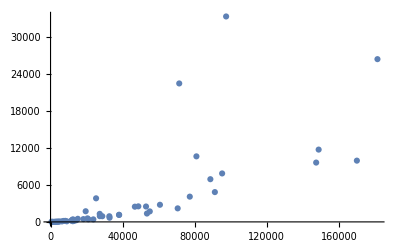

```mathematica
ListPlot[MapThread[{#1,#2}&,{display[[All,3]],TimeInSeconds}],PlotRange->All]
```

We plot a nice (albeit convoluted) summarizing table of all of the chiral equivalence classes (as defined on the top of pg. 17) we really care about. Rows are equivalence classes, sorted by number of BSM chiral particles. Columns are BSM chiral content (# of terms,  irrep, hypercharge), # of BSM chiral particles, # of different elements in the equivalence class (i.e., configurations of BSM vector-like particles which can appear with the given BSM chiral particles), TABLE} where the columns of TABLE are individual BSM vector-like particle configurations (i.e., elements of the equivalence class). The rows of each column in TABLE is the NAB, the BSM vector-like particles (# of terms,  irrep, hypercharge), the number of unique hypercharges which give rise to this model, and an exhaustive list of the hypercharges which give rise to the model (going from  to  from left to right).

```mathematica
modelInfoDisplay[[;;13]]
```

({} | 0 | 9 | ({4,3,3} | {5,3,3} | {4,6,3} | {7,3,3} | {7,3,3} | {7,3,3} | {7,3,3} | {7,3,3} | {5,6,3}
(3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
7 | (1,1) | 1/2
7 | (1,1) | -1/2
4 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
5 | (1,2) | 1/2
5 | (1,2) | -1/2
8 | (1,2) | 0
11 | (1,1) | 1/2
11 | (1,1) | -1/2
11 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
7 | (1,1) | 1
7 | (1,1) | -1
18 | (1,1) | 1/2
18 | (1,1) | -1/2
22 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
16 | (1,2) | 0
19 | (1,1) | 1/2
19 | (1,1) | -1/2
25 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
10 | (1,2) | 1/2
10 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 1
3 | (1,1) | -1
19 | (1,1) | 1/2
19 | (1,1) | -1/2
19 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 1
3 | (1,2) | -1
7 | (1,2) | 1/2
7 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 3/2
3 | (1,1) | -3/2
6 | (1,1) | 1
6 | (1,1) | -1
16 | (1,1) | 1/2
16 | (1,1) | -1/2
13 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 3/2
3 | (1,2) | -3/2
7 | (1,2) | 1/2
7 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 2
3 | (1,1) | -2
6 | (1,1) | 3/2
6 | (1,1) | -3/2
3 | (1,1) | 1
3 | (1,1) | -1
13 | (1,1) | 1/2
13 | (1,1) | -1/2
13 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
10 | (1,2) | 0
3 | (1,1) | 3/5
3 | (1,1) | -3/5
13 | (1,1) | 1/2
13 | (1,1) | -1/2
3 | (1,1) | 2/5
3 | (1,1) | -2/5
6 | (1,1) | 1/10
6 | (1,1) | -1/10
13 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
5 | (1,2) | 1/2
5 | (1,2) | -1/2
8 | (1,2) | 0
8 | (1,1) | 1
8 | (1,1) | -1
30 | (1,1) | 1/2
30 | (1,1) | -1/2
38 | (1,1) | 0)
6 | 18 | 60 | 18 | 18 | 36 | 36 | 6 | 72
(1/6 | 0 | 1/4 | -1/4
1/6 | 0 | 0 | -1/2
1/6 | 0 | -1/4 | 1/4
1/6 | 0 | -1/4 | -1/4
1/6 | 0 | 0 | 1/2
1/6 | 0 | 1/4 | 1/4) | (0 | 1/6 | 0 | 1/4 | -1/4
0 | 1/6 | 0 | 0 | -1/2
0 | 1/6 | 0 | -1/4 | 1/4
0 | 1/6 | 0 | -1/4 | -1/4
0 | 1/6 | 0 | 0 | 1/2
0 | 1/6 | 0 | 1/4 | 1/4
1/8 | 1/24 | 0 | 1/4 | -1/4
1/8 | 1/24 | 0 | 0 | -1/2
1/8 | 1/24 | 0 | -1/4 | 1/4
1/8 | 1/24 | 0 | -1/4 | -1/4
1/8 | 1/24 | 0 | 0 | 1/2
1/8 | 1/24 | 0 | 1/4 | 1/4) | (1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | -1/4
1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | -1/4
1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | -1/4
1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | -1/4
1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | -1/4
1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | -1/4
1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | -1/2
1/6 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
1/6 | 0 | 1/8 | -1/8 | 0 | 0 | -1/2
1/6 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
1/6 | 1/10 | -1/10 | 0 | 0 | 0 | -1/2
1/6 | 0 | -1/8 | 1/8 | 0 | 0 | -1/2
1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | -1/2
1/6 | -1/10 | 1/10 | 0 | 0 | 0 | -1/2
1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | 1/4
1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | 1/4
1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | 1/4
1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | 1/4
1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | 1/4
1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | 1/4
1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | -1/4
1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | -1/4
1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | -1/4
1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | -1/4
1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | -1/4
1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | -1/4
1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | 1/2
1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
1/6 | 0 | 1/8 | -1/8 | 0 | 0 | 1/2
1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
1/6 | 1/10 | -1/10 | 0 | 0 | 0 | 1/2
1/6 | 0 | -1/8 | 1/8 | 0 | 0 | 1/2
1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | 1/2
1/6 | -1/10 | 1/10 | 0 | 0 | 0 | 1/2
1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | 1/4
1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | 1/4
1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4
1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | 1/4
1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | 1/4
1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | 1/4
1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | 1/4) | (0 | 0 | 0 | 1/6 | 0 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | -1/2
0 | 0 | 0 | 1/6 | 0 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 1/2
0 | 0 | 0 | 1/6 | 0 | 1/4 | 1/4
0 | 0 | 1/8 | 1/24 | 0 | 1/4 | -1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/2
0 | 0 | 1/8 | 1/24 | 0 | -1/4 | 1/4
0 | 0 | 1/8 | 1/24 | 0 | -1/4 | -1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/2
0 | 0 | 1/8 | 1/24 | 0 | 1/4 | 1/4) | (0 | 1/10 | -1/10 | 1/6 | 0 | 1/4 | -1/4
0 | -1/10 | 1/10 | 1/6 | 0 | 1/4 | -1/4
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | -1/2
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | -1/2
0 | 1/10 | -1/10 | 1/6 | 0 | -1/4 | 1/4
0 | -1/10 | 1/10 | 1/6 | 0 | -1/4 | 1/4
0 | 1/10 | -1/10 | 1/6 | 0 | -1/4 | -1/4
0 | -1/10 | 1/10 | 1/6 | 0 | -1/4 | -1/4
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 1/2
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 1/2
0 | 1/10 | -1/10 | 1/6 | 0 | 1/4 | 1/4
0 | -1/10 | 1/10 | 1/6 | 0 | 1/4 | 1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 1/4 | -1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | -1/2
0 | 1/10 | 3/20 | -1/12 | 0 | -1/4 | 1/4
0 | 1/10 | 3/20 | -1/12 | 0 | -1/4 | -1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 1/2
0 | 1/10 | 3/20 | -1/12 | 0 | 1/4 | 1/4) | (0 | 1/5 | -1/5 | 1/6 | 0 | 1/4 | -1/4
0 | -1/5 | 1/5 | 1/6 | 0 | 1/4 | -1/4
0 | 1/5 | -1/5 | 1/6 | 0 | 0 | -1/2
0 | -1/5 | 1/5 | 1/6 | 0 | 0 | -1/2
0 | 1/5 | -1/5 | 1/6 | 0 | -1/4 | 1/4
0 | -1/5 | 1/5 | 1/6 | 0 | -1/4 | 1/4
0 | 1/5 | -1/5 | 1/6 | 0 | -1/4 | -1/4
0 | -1/5 | 1/5 | 1/6 | 0 | -1/4 | -1/4
0 | 1/5 | -1/5 | 1/6 | 0 | 0 | 1/2
0 | -1/5 | 1/5 | 1/6 | 0 | 0 | 1/2
0 | 1/5 | -1/5 | 1/6 | 0 | 1/4 | 1/4
0 | -1/5 | 1/5 | 1/6 | 0 | 1/4 | 1/4
0 | 1/5 | 7/40 | -5/24 | 0 | 1/4 | -1/4
0 | -1/5 | 3/40 | 7/24 | 0 | 1/4 | -1/4
0 | 1/5 | 7/40 | -5/24 | 0 | 0 | -1/2
0 | -1/5 | 3/40 | 7/24 | 0 | 0 | -1/2
0 | 1/5 | 7/40 | -5/24 | 0 | -1/4 | 1/4
0 | -1/5 | 3/40 | 7/24 | 0 | -1/4 | 1/4
0 | 1/5 | 7/40 | -5/24 | 0 | -1/4 | -1/4
0 | -1/5 | 3/40 | 7/24 | 0 | -1/4 | -1/4
0 | 1/5 | 7/40 | -5/24 | 0 | 0 | 1/2
0 | -1/5 | 3/40 | 7/24 | 0 | 0 | 1/2
0 | 1/5 | 7/40 | -5/24 | 0 | 1/4 | 1/4
0 | -1/5 | 3/40 | 7/24 | 0 | 1/4 | 1/4
0 | 1/10 | 11/40 | -5/24 | 0 | 1/4 | -1/4
0 | 1/10 | -9/40 | 7/24 | 0 | 1/4 | -1/4
0 | 1/10 | 11/40 | -5/24 | 0 | 0 | -1/2
0 | 1/10 | -9/40 | 7/24 | 0 | 0 | -1/2
0 | 1/10 | 11/40 | -5/24 | 0 | -1/4 | 1/4
0 | 1/10 | -9/40 | 7/24 | 0 | -1/4 | 1/4
0 | 1/10 | 11/40 | -5/24 | 0 | -1/4 | -1/4
0 | 1/10 | -9/40 | 7/24 | 0 | -1/4 | -1/4
0 | 1/10 | 11/40 | -5/24 | 0 | 0 | 1/2
0 | 1/10 | -9/40 | 7/24 | 0 | 0 | 1/2
0 | 1/10 | 11/40 | -5/24 | 0 | 1/4 | 1/4
0 | 1/10 | -9/40 | 7/24 | 0 | 1/4 | 1/4) | (0 | 3/10 | -3/10 | 1/6 | 0 | 1/4 | -1/4
0 | -3/10 | 3/10 | 1/6 | 0 | 1/4 | -1/4
0 | 3/10 | -3/10 | 1/6 | 0 | 0 | -1/2
0 | -3/10 | 3/10 | 1/6 | 0 | 0 | -1/2
0 | 3/10 | -3/10 | 1/6 | 0 | -1/4 | 1/4
0 | -3/10 | 3/10 | 1/6 | 0 | -1/4 | 1/4
0 | 3/10 | -3/10 | 1/6 | 0 | -1/4 | -1/4
0 | -3/10 | 3/10 | 1/6 | 0 | -1/4 | -1/4
0 | 3/10 | -3/10 | 1/6 | 0 | 0 | 1/2
0 | -3/10 | 3/10 | 1/6 | 0 | 0 | 1/2
0 | 3/10 | -3/10 | 1/6 | 0 | 1/4 | 1/4
0 | -3/10 | 3/10 | 1/6 | 0 | 1/4 | 1/4
0 | 3/10 | 1/5 | -1/3 | 0 | 1/4 | -1/4
0 | -3/10 | 1/20 | 5/12 | 0 | 1/4 | -1/4
0 | 3/10 | 1/5 | -1/3 | 0 | 0 | -1/2
0 | -3/10 | 1/20 | 5/12 | 0 | 0 | -1/2
0 | 3/10 | 1/5 | -1/3 | 0 | -1/4 | 1/4
0 | -3/10 | 1/20 | 5/12 | 0 | -1/4 | 1/4
0 | 3/10 | 1/5 | -1/3 | 0 | -1/4 | -1/4
0 | -3/10 | 1/20 | 5/12 | 0 | -1/4 | -1/4
0 | 3/10 | 1/5 | -1/3 | 0 | 0 | 1/2
0 | -3/10 | 1/20 | 5/12 | 0 | 0 | 1/2
0 | 3/10 | 1/5 | -1/3 | 0 | 1/4 | 1/4
0 | -3/10 | 1/20 | 5/12 | 0 | 1/4 | 1/4
0 | 1/10 | 2/5 | -1/3 | 0 | 1/4 | -1/4
0 | 1/10 | -7/20 | 5/12 | 0 | 1/4 | -1/4
0 | 1/10 | 2/5 | -1/3 | 0 | 0 | -1/2
0 | 1/10 | -7/20 | 5/12 | 0 | 0 | -1/2
0 | 1/10 | 2/5 | -1/3 | 0 | -1/4 | 1/4
0 | 1/10 | -7/20 | 5/12 | 0 | -1/4 | 1/4
0 | 1/10 | 2/5 | -1/3 | 0 | -1/4 | -1/4
0 | 1/10 | -7/20 | 5/12 | 0 | -1/4 | -1/4
0 | 1/10 | 2/5 | -1/3 | 0 | 0 | 1/2
0 | 1/10 | -7/20 | 5/12 | 0 | 0 | 1/2
0 | 1/10 | 2/5 | -1/3 | 0 | 1/4 | 1/4
0 | 1/10 | -7/20 | 5/12 | 0 | 1/4 | 1/4) | (0 | 1/10 | 0 | 1/15 | 0 | 1/4 | -1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/2
0 | 1/10 | 0 | 1/15 | 0 | -1/4 | 1/4
0 | 1/10 | 0 | 1/15 | 0 | -1/4 | -1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/2
0 | 1/10 | 0 | 1/15 | 0 | 1/4 | 1/4) | (0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | -1/4
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | -1/4
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | -1/4
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | -1/4
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | -1/4
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | -1/4
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | -1/2
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 0 | -1/2
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 0 | -1/2
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 0 | -1/2
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | -1/2
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 0 | -1/2
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | 1/4
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | 1/4
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | 1/4
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | 1/4
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | 1/4
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | 1/4
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | -1/4
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | -1/4
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | -1/4
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | -1/4
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | -1/4
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | -1/4
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | 1/2
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 0 | 1/2
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 0 | 1/2
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 0 | 1/2
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | 1/2
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 0 | 1/2
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | 1/4
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | 1/4
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | 1/4
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | 1/4
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | 1/4
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | 1/4
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4))
(1 | (1,2) | 3/2
3 | (1,2) | -1/2
1 | (1,1) | -2
2 | (1,1) | 1) | 11 | 1 | ({7,3,3}
(3 | (3,1) | 5/3
3 | (OverBar[3],1) | -5/3
6 | (1,2) | 3/2
6 | (1,2) | -3/2
7 | (1,2) | 1/2
7 | (1,2) | -1/2
6 | (1,1) | 2
6 | (1,1) | -2
13 | (1,1) | 1
13 | (1,1) | -1
22 | (1,1) | 0)
24
(0 | 1/5 | 3/10 | 1/6 | 1/2 | 0 | -1
0 | 1/5 | 3/10 | 1/6 | 1/2 | 1/2 | -1/2
0 | 1/5 | 3/10 | 1/6 | 1/2 | -1/2 | -1/2
0 | 1/5 | 3/10 | 1/6 | 1/2 | -1/2 | 1/2
0 | 1/5 | 3/10 | 1/6 | 1/2 | 1/2 | 1/2
0 | 1/5 | 3/10 | 1/6 | 1/2 | 0 | 1
0 | 1/5 | 1/20 | 5/12 | 1/2 | 0 | -1
0 | 1/5 | 1/20 | 5/12 | 1/2 | 1/2 | -1/2
0 | 1/5 | 1/20 | 5/12 | 1/2 | -1/2 | -1/2
0 | 1/5 | 1/20 | 5/12 | 1/2 | -1/2 | 1/2
0 | 1/5 | 1/20 | 5/12 | 1/2 | 1/2 | 1/2
0 | 1/5 | 1/20 | 5/12 | 1/2 | 0 | 1
0 | 0 | 1/4 | 5/12 | 1/2 | 0 | -1
0 | 0 | 1/4 | 5/12 | 1/2 | 1/2 | -1/2
0 | 0 | 1/4 | 5/12 | 1/2 | -1/2 | -1/2
0 | 0 | 1/4 | 5/12 | 1/2 | -1/2 | 1/2
0 | 0 | 1/4 | 5/12 | 1/2 | 1/2 | 1/2
0 | 0 | 1/4 | 5/12 | 1/2 | 0 | 1))
(1 | (1,2) | -1/2
3 | (1,2) | 1/6
1 | (1,1) | 1
3 | (1,1) | -2/3
3 | (1,1) | 1/3) | 15 | 5 | ({4,3,3} | {7,3,3} | {7,3,3} | {7,3,3} | {7,3,3}
(3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
4 | (1,2) | 1/2
4 | (1,2) | -1/2
3 | (1,1) | 1/3
3 | (1,1) | -1/3
5 | (1,1) | 0) | (3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
13 | (1,2) | 1/2
13 | (1,2) | -1/2
9 | (1,1) | 1
9 | (1,1) | -1
3 | (1,1) | 1/3
3 | (1,1) | -1/3
32 | (1,1) | 0) | (3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
3 | (1,2) | 3/2
3 | (1,2) | -3/2
10 | (1,2) | 1/2
10 | (1,2) | -1/2
6 | (1,1) | 2
6 | (1,1) | -2
9 | (1,1) | 1
9 | (1,1) | -1
3 | (1,1) | 1/3
3 | (1,1) | -1/3
20 | (1,1) | 0) | (3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
10 | (1,2) | 1/2
10 | (1,2) | -1/2
3 | (1,2) | 1/6
3 | (1,2) | -1/6
3 | (1,1) | 1
3 | (1,1) | -1
6 | (1,1) | 2/3
6 | (1,1) | -2/3
9 | (1,1) | 1/3
9 | (1,1) | -1/3
20 | (1,1) | 0) | (3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
10 | (1,2) | 1/2
10 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
3 | (1,1) | 1
3 | (1,1) | -1
6 | (1,1) | 3/5
6 | (1,1) | -3/5
6 | (1,1) | 2/5
6 | (1,1) | -2/5
3 | (1,1) | 1/3
3 | (1,1) | -1/3
20 | (1,1) | 0)
3 | 9 | 21 | 6 | 3
(0 | -1/6 | 1/3 | 0
0 | -1/6 | -1/6 | 1/2
0 | -1/6 | -1/6 | -1/2) | (0 | -1/15 | -1/10 | 1/6 | -1/6 | 1/3 | 0
0 | -1/15 | -1/10 | 1/6 | -1/6 | -1/6 | -1/2
0 | -1/15 | -1/10 | 1/6 | -1/6 | -1/6 | 1/2
0 | -1/15 | 3/20 | -1/12 | -1/6 | 1/3 | 0
0 | -1/15 | 3/20 | -1/12 | -1/6 | -1/6 | -1/2
0 | -1/15 | 3/20 | -1/12 | -1/6 | -1/6 | 1/2
0 | 2/15 | -1/20 | -1/12 | -1/6 | 1/3 | 0
0 | 2/15 | -1/20 | -1/12 | -1/6 | -1/6 | -1/2
0 | 2/15 | -1/20 | -1/12 | -1/6 | -1/6 | 1/2) | (0 | 1/3 | 0 | -1/3 | -1/6 | 1/3 | 0
0 | 1/3 | -1/4 | -1/12 | -1/6 | 1/3 | 0
0 | -1/15 | 2/5 | -1/3 | -1/6 | 1/3 | 0
0 | -4/15 | 7/20 | -1/12 | -1/6 | 1/3 | 0
0 | -1/15 | -7/20 | 5/12 | -1/6 | 1/3 | 0
0 | -4/15 | -3/20 | 5/12 | -1/6 | 1/3 | 0
0 | 1/3 | 0 | -1/3 | -1/6 | -1/6 | 1/2
0 | 1/3 | -1/4 | -1/12 | -1/6 | -1/6 | 1/2
0 | -1/15 | 2/5 | -1/3 | -1/6 | -1/6 | 1/2
0 | -4/15 | 7/20 | -1/12 | -1/6 | -1/6 | 1/2
0 | -1/15 | -7/20 | 5/12 | -1/6 | -1/6 | 1/2
0 | -4/15 | -3/20 | 5/12 | -1/6 | -1/6 | 1/2
0 | 1/3 | 0 | -1/3 | -1/6 | -1/6 | -1/2
0 | 1/3 | -1/4 | -1/12 | -1/6 | -1/6 | -1/2
0 | -1/15 | 2/5 | -1/3 | -1/6 | -1/6 | -1/2
0 | -4/15 | 7/20 | -1/12 | -1/6 | -1/6 | -1/2
0 | -1/15 | -7/20 | 5/12 | -1/6 | -1/6 | -1/2
0 | -4/15 | -3/20 | 5/12 | -1/6 | -1/6 | -1/2) | (0 | 0 | -1/12 | 1/12 | -1/6 | 1/3 | 0
0 | 0 | 1/12 | -1/12 | -1/6 | 1/3 | 0
0 | 0 | -1/12 | 1/12 | -1/6 | -1/6 | 1/2
0 | 0 | 1/12 | -1/12 | -1/6 | -1/6 | 1/2
0 | 0 | -1/12 | 1/12 | -1/6 | -1/6 | -1/2
0 | 0 | 1/12 | -1/12 | -1/6 | -1/6 | -1/2) | (0 | -1/15 | 0 | 1/15 | -1/6 | 1/3 | 0
0 | -1/15 | 0 | 1/15 | -1/6 | -1/6 | 1/2
0 | -1/15 | 0 | 1/15 | -1/6 | -1/6 | -1/2))
(1 | (3,2) | 1/6
1 | (OverBar[3],1) | -2/3
1 | (OverBar[3],1) | 1/3
1 | (1,2) | -1/2
1 | (1,1) | 1) | 15 | 9 | ({5,4,4} | {5,4,4} | {5,4,4} | {5,4,4} | {7,4,4} | {7,4,4} | {7,4,4} | {7,4,4} | {7,4,4}
(8 | (3,1) | 1/6
8 | (OverBar[3],1) | -1/6
5 | (1,2) | 1/2
5 | (1,2) | -1/2
14 | (1,2) | 0
22 | (1,1) | 1/2
22 | (1,1) | -1/2
37 | (1,1) | 0) | (4 | (3,1) | 2/3
4 | (OverBar[3],1) | -2/3
4 | (OverBar[3],1) | 1/3
4 | (3,1) | -1/3
10 | (1,2) | 1/2
10 | (1,2) | -1/2
4 | (1,2) | 0
14 | (1,1) | 1
14 | (1,1) | -1
12 | (1,1) | 1/2
12 | (1,1) | -1/2
29 | (1,1) | 0) | (4 | (3,1) | 7/6
4 | (OverBar[3],1) | -7/6
4 | (OverBar[3],1) | 5/6
4 | (3,1) | -5/6
5 | (1,2) | 1
5 | (1,2) | -1
5 | (1,2) | 1/2
5 | (1,2) | -1/2
4 | (1,2) | 0
5 | (1,1) | 2
5 | (1,1) | -2
9 | (1,1) | 3/2
9 | (1,1) | -3/2
8 | (1,1) | 1
8 | (1,1) | -1
13 | (1,1) | 1/2
13 | (1,1) | -1/2
11 | (1,1) | 0) | (4 | (3,1) | 5/3
4 | (OverBar[3],1) | -5/3
4 | (OverBar[3],1) | 4/3
4 | (3,1) | -4/3
5 | (1,2) | 3/2
5 | (1,2) | -3/2
5 | (1,2) | 1/2
5 | (1,2) | -1/2
4 | (1,2) | 0
5 | (1,1) | 3
5 | (1,1) | -3
9 | (1,1) | 2
9 | (1,1) | -2
8 | (1,1) | 3/2
8 | (1,1) | -3/2
9 | (1,1) | 1
9 | (1,1) | -1
4 | (1,1) | 1/2
4 | (1,1) | -1/2
11 | (1,1) | 0) | (8 | (3,1) | 1/6
8 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
26 | (1,2) | 0
34 | (1,1) | 1/2
34 | (1,1) | -1/2
77 | (1,1) | 0) | (8 | (3,1) | 1/6
8 | (OverBar[3],1) | -1/6
11 | (1,2) | 1/2
11 | (1,2) | -1/2
18 | (1,2) | 0
4 | (1,1) | 1
4 | (1,1) | -1
42 | (1,1) | 1/2
42 | (1,1) | -1/2
53 | (1,1) | 0) | (4 | (3,1) | 2/3
4 | (OverBar[3],1) | -2/3
4 | (OverBar[3],1) | 1/3
4 | (3,1) | -1/3
14 | (1,2) | 1/2
14 | (1,2) | -1/2
12 | (1,2) | 0
18 | (1,1) | 1
18 | (1,1) | -1
36 | (1,1) | 1/2
36 | (1,1) | -1/2
37 | (1,1) | 0) | (4 | (3,1) | 7/6
4 | (OverBar[3],1) | -7/6
4 | (OverBar[3],1) | 5/6
4 | (3,1) | -5/6
7 | (1,2) | 1
7 | (1,2) | -1
7 | (1,2) | 1/2
7 | (1,2) | -1/2
12 | (1,2) | 0
7 | (1,1) | 2
7 | (1,1) | -2
11 | (1,1) | 3/2
11 | (1,1) | -3/2
24 | (1,1) | 1
24 | (1,1) | -1
23 | (1,1) | 1/2
23 | (1,1) | -1/2
15 | (1,1) | 0) | (4 | (3,1) | 5/3
4 | (OverBar[3],1) | -5/3
4 | (OverBar[3],1) | 4/3
4 | (3,1) | -4/3
7 | (1,2) | 3/2
7 | (1,2) | -3/2
7 | (1,2) | 1/2
7 | (1,2) | -1/2
12 | (1,2) | 0
7 | (1,1) | 3
7 | (1,1) | -3
11 | (1,1) | 2
11 | (1,1) | -2
24 | (1,1) | 3/2
24 | (1,1) | -3/2
11 | (1,1) | 1
11 | (1,1) | -1
12 | (1,1) | 1/2
12 | (1,1) | -1/2
15 | (1,1) | 0)
20 | 12 | 48 | 48 | 20 | 24 | 12 | 48 | 48
(0 | 1/6 | 0 | 0 | 0 | 1/4 | -1/4
0 | 1/6 | 0 | 0 | 1/6 | 1/12 | -1/4
0 | 1/6 | 0 | 0 | 0 | 0 | -1/2
0 | 1/6 | 0 | 0 | 0 | -1/4 | 1/4
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0
0 | 1/6 | 0 | 0 | 0 | -1/4 | -1/4
0 | 1/6 | 0 | 0 | -1/6 | -1/12 | 1/4
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0
0 | 1/6 | 0 | 0 | -1/6 | -1/12 | -1/4
0 | 1/6 | 0 | 0 | 0 | 0 | 1/2
0 | 1/6 | 0 | 0 | 0 | 1/4 | 1/4
0 | 1/6 | 0 | 0 | 1/6 | 1/12 | 1/4) | (0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | -1/2
0 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/2
0 | 1/6 | 1/6 | -1/6 | 1/6 | 1/3 | 0
0 | 1/6 | -1/6 | 1/6 | 1/6 | 1/3 | 0
0 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/2
0 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/2
0 | 1/6 | 1/6 | -1/6 | -1/6 | -1/3 | 0
0 | 1/6 | -1/6 | 1/6 | -1/6 | -1/3 | 0
0 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/2
0 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/2
0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/2
0 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/2) | (0 | 1/6 | -1/3 | 1/3 | -1/3 | 1/12 | -3/4
0 | 1/6 | 1/3 | -1/3 | -1/3 | 1/12 | -3/4
0 | 1/6 | 1/3 | -1/3 | 1/3 | 5/12 | 1/4
0 | 1/6 | -1/3 | 1/3 | 1/3 | 5/12 | 1/4
0 | 1/6 | -1/3 | 1/3 | 1/6 | -5/12 | -3/4
0 | 1/6 | 1/3 | -1/3 | 1/6 | -5/12 | -3/4
0 | 1/6 | 1/3 | -1/3 | 1/6 | 7/12 | 1/4
0 | 1/6 | -1/3 | 1/3 | 1/6 | 7/12 | 1/4
0 | 1/6 | -1/3 | 1/3 | 1/3 | -1/3 | -1/2
0 | 1/6 | 1/3 | -1/3 | 1/3 | -1/3 | -1/2
0 | 1/6 | 1/3 | -1/3 | -1/3 | 1/3 | -1/2
0 | 1/6 | -1/3 | 1/3 | -1/3 | 1/3 | -1/2
0 | 1/6 | -1/3 | 1/3 | -1/3 | -5/12 | -1/4
0 | 1/6 | 1/3 | -1/3 | -1/3 | -5/12 | -1/4
0 | 1/6 | 1/3 | -1/3 | 1/3 | -1/12 | 3/4
0 | 1/6 | -1/3 | 1/3 | 1/3 | -1/12 | 3/4
0 | 1/6 | -1/3 | 1/3 | 1/6 | -1/6 | -1
0 | 1/6 | 1/3 | -1/3 | 1/6 | -1/6 | -1
0 | 1/6 | 1/3 | -1/3 | 1/6 | -1/6 | 1
0 | 1/6 | -1/3 | 1/3 | 1/6 | -1/6 | 1
0 | 1/6 | -1/3 | 1/3 | 1/3 | -1/12 | -3/4
0 | 1/6 | 1/3 | -1/3 | 1/3 | -1/12 | -3/4
0 | 1/6 | 1/3 | -1/3 | -1/3 | -5/12 | 1/4
0 | 1/6 | -1/3 | 1/3 | -1/3 | -5/12 | 1/4
0 | 1/6 | -1/3 | 1/3 | -1/6 | -7/12 | -1/4
0 | 1/6 | 1/3 | -1/3 | -1/6 | -7/12 | -1/4
0 | 1/6 | 1/3 | -1/3 | -1/6 | 5/12 | 3/4
0 | 1/6 | -1/3 | 1/3 | -1/6 | 5/12 | 3/4
0 | 1/6 | -1/3 | 1/3 | -1/6 | 1/6 | -1
0 | 1/6 | 1/3 | -1/3 | -1/6 | 1/6 | -1
0 | 1/6 | 1/3 | -1/3 | -1/6 | 1/6 | 1
0 | 1/6 | -1/3 | 1/3 | -1/6 | 1/6 | 1
0 | 1/6 | -1/3 | 1/3 | -1/6 | 5/12 | -3/4
0 | 1/6 | 1/3 | -1/3 | -1/6 | 5/12 | -3/4
0 | 1/6 | 1/3 | -1/3 | -1/6 | -7/12 | 1/4
0 | 1/6 | -1/3 | 1/3 | -1/6 | -7/12 | 1/4
0 | 1/6 | -1/3 | 1/3 | 1/3 | -1/3 | 1/2
0 | 1/6 | 1/3 | -1/3 | 1/3 | -1/3 | 1/2
0 | 1/6 | 1/3 | -1/3 | -1/3 | 1/3 | 1/2
0 | 1/6 | -1/3 | 1/3 | -1/3 | 1/3 | 1/2
0 | 1/6 | -1/3 | 1/3 | 1/3 | 5/12 | -1/4
0 | 1/6 | 1/3 | -1/3 | 1/3 | 5/12 | -1/4
0 | 1/6 | 1/3 | -1/3 | -1/3 | 1/12 | 3/4
0 | 1/6 | -1/3 | 1/3 | -1/3 | 1/12 | 3/4
0 | 1/6 | -1/3 | 1/3 | 1/6 | 7/12 | -1/4
0 | 1/6 | 1/3 | -1/3 | 1/6 | 7/12 | -1/4
0 | 1/6 | 1/3 | -1/3 | 1/6 | -5/12 | 3/4
0 | 1/6 | -1/3 | 1/3 | 1/6 | -5/12 | 3/4) | (0 | 1/6 | 1/2 | -1/2 | 1/2 | 1/2 | 1/2
0 | 1/6 | 1/2 | -1/2 | -1/2 | 0 | -1
0 | 1/6 | -1/2 | 1/2 | -1/2 | 0 | -1
0 | 1/6 | -1/2 | 1/2 | 1/2 | 1/2 | 1/2
0 | 1/6 | 1/2 | -1/2 | 1/6 | 5/6 | 1/2
0 | 1/6 | 1/2 | -1/2 | 1/6 | -2/3 | -1
0 | 1/6 | -1/2 | 1/2 | 1/6 | -2/3 | -1
0 | 1/6 | -1/2 | 1/2 | 1/6 | 5/6 | 1/2
0 | 1/6 | 1/2 | -1/2 | -1/2 | 1/2 | -1/2
0 | 1/6 | 1/2 | -1/2 | 1/2 | -1/2 | -1/2
0 | 1/6 | -1/2 | 1/2 | 1/2 | -1/2 | -1/2
0 | 1/6 | -1/2 | 1/2 | -1/2 | 1/2 | -1/2
0 | 1/6 | 1/2 | -1/2 | 1/2 | 0 | 1
0 | 1/6 | 1/2 | -1/2 | -1/2 | -1/2 | -1/2
0 | 1/6 | -1/2 | 1/2 | -1/2 | -1/2 | -1/2
0 | 1/6 | -1/2 | 1/2 | 1/2 | 0 | 1
0 | 1/6 | 1/2 | -1/2 | 1/6 | -1/6 | 3/2
0 | 1/6 | 1/2 | -1/2 | 1/6 | -1/6 | -3/2
0 | 1/6 | -1/2 | 1/2 | 1/6 | -1/6 | -3/2
0 | 1/6 | -1/2 | 1/2 | 1/6 | -1/6 | 3/2
0 | 1/6 | 1/2 | -1/2 | -1/2 | -1/2 | 1/2
0 | 1/6 | 1/2 | -1/2 | 1/2 | 0 | -1
0 | 1/6 | -1/2 | 1/2 | 1/2 | 0 | -1
0 | 1/6 | -1/2 | 1/2 | -1/2 | -1/2 | 1/2
0 | 1/6 | 1/2 | -1/2 | -1/6 | 2/3 | 1
0 | 1/6 | 1/2 | -1/2 | -1/6 | -5/6 | -1/2
0 | 1/6 | -1/2 | 1/2 | -1/6 | -5/6 | -1/2
0 | 1/6 | -1/2 | 1/2 | -1/6 | 2/3 | 1
0 | 1/6 | 1/2 | -1/2 | -1/6 | 1/6 | 3/2
0 | 1/6 | 1/2 | -1/2 | -1/6 | 1/6 | -3/2
0 | 1/6 | -1/2 | 1/2 | -1/6 | 1/6 | -3/2
0 | 1/6 | -1/2 | 1/2 | -1/6 | 1/6 | 3/2
0 | 1/6 | 1/2 | -1/2 | -1/6 | -5/6 | 1/2
0 | 1/6 | 1/2 | -1/2 | -1/6 | 2/3 | -1
0 | 1/6 | -1/2 | 1/2 | -1/6 | 2/3 | -1
0 | 1/6 | -1/2 | 1/2 | -1/6 | -5/6 | 1/2
0 | 1/6 | 1/2 | -1/2 | -1/2 | 1/2 | 1/2
0 | 1/6 | 1/2 | -1/2 | 1/2 | -1/2 | 1/2
0 | 1/6 | -1/2 | 1/2 | 1/2 | -1/2 | 1/2
0 | 1/6 | -1/2 | 1/2 | -1/2 | 1/2 | 1/2
0 | 1/6 | 1/2 | -1/2 | -1/2 | 0 | 1
0 | 1/6 | 1/2 | -1/2 | 1/2 | 1/2 | -1/2
0 | 1/6 | -1/2 | 1/2 | 1/2 | 1/2 | -1/2
0 | 1/6 | -1/2 | 1/2 | -1/2 | 0 | 1
0 | 1/6 | 1/2 | -1/2 | 1/6 | -2/3 | 1
0 | 1/6 | 1/2 | -1/2 | 1/6 | 5/6 | -1/2
0 | 1/6 | -1/2 | 1/2 | 1/6 | 5/6 | -1/2
0 | 1/6 | -1/2 | 1/2 | 1/6 | -2/3 | 1) | (0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | 1/12 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -1/2
0 | 0 | 0 | 1/6 | 0 | 0 | 0 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0
0 | 0 | 0 | 1/6 | 0 | 0 | 0 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | -1/12 | 1/4
0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0
0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | -1/12 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | 1/12 | 1/4) | (0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 0 | 1/4 | -1/4
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 0 | 1/4 | -1/4
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 0 | 0 | -1/2
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 0 | 0 | -1/2
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 0 | -1/4 | 1/4
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 0 | -1/4 | 1/4
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 0 | -1/4 | -1/4
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 0 | -1/4 | -1/4
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 0 | 0 | 1/2
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 0 | 0 | 1/2
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 0 | 1/4 | 1/4
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 0 | 1/4 | 1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 0 | 1/4 | -1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 0 | 0 | -1/2
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 0 | -1/4 | 1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 1/6 | -1/6 | 0
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 0 | -1/4 | -1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | -1/6 | 1/6 | 0
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 0 | 0 | 1/2
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 0 | 1/4 | 1/4) | (0 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | -1/2
0 | 0 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/2
0 | 0 | 0 | 1/6 | 1/6 | -1/6 | 1/6 | 1/3 | 0
0 | 0 | 0 | 1/6 | -1/6 | 1/6 | 1/6 | 1/3 | 0
0 | 0 | 0 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/2
0 | 0 | 0 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/2
0 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | -1/3 | 0
0 | 0 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | -1/3 | 0
0 | 0 | 0 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/2
0 | 0 | 0 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/2
0 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/2
0 | 0 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/2) | (0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/3 | 1/12 | -3/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/3 | 1/12 | -3/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/3 | 5/12 | 1/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/3 | 5/12 | 1/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | -5/12 | -3/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/6 | -5/12 | -3/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/6 | 7/12 | 1/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | 7/12 | 1/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/3 | -1/3 | -1/2
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/3 | -1/3 | -1/2
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/3 | 1/3 | -1/2
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/3 | 1/3 | -1/2
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/3 | -5/12 | -1/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/3 | -5/12 | -1/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/3 | -1/12 | 3/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/3 | -1/12 | 3/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | -1/6 | -1
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/6 | -1/6 | -1
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/6 | -1/6 | 1
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | -1/6 | 1
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/3 | -1/12 | -3/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/3 | -1/12 | -3/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/3 | -5/12 | 1/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/3 | -5/12 | 1/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | -7/12 | -1/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | -7/12 | -1/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | 5/12 | 3/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | 5/12 | 3/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | 1/6 | -1
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | 1/6 | -1
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | 1/6 | 1
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | 1/6 | 1
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | 5/12 | -3/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | 5/12 | -3/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | -7/12 | 1/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | -7/12 | 1/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/3 | -1/3 | 1/2
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/3 | -1/3 | 1/2
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/3 | 1/3 | 1/2
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/3 | 1/3 | 1/2
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/3 | 5/12 | -1/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/3 | 5/12 | -1/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/3 | 1/12 | 3/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/3 | 1/12 | 3/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | 7/12 | -1/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/6 | 7/12 | -1/4
0 | 0 | 0 | 1/6 | 1/3 | -1/3 | 1/6 | -5/12 | 3/4
0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | -5/12 | 3/4) | (0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/2 | 1/2 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/2 | 0 | -1
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/2 | 0 | -1
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/2 | 1/2 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/6 | 5/6 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/6 | -2/3 | -1
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/6 | -2/3 | -1
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/6 | 5/6 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/2 | 1/2 | -1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/2 | -1/2 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/2 | -1/2 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/2 | 1/2 | -1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/2 | 0 | 1
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/2 | -1/2 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/2 | -1/2 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/2 | 0 | 1
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/6 | -1/6 | 3/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/6 | -1/6 | -3/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/6 | -1/6 | -3/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/6 | -1/6 | 3/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/2 | -1/2 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/2 | 0 | -1
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/2 | 0 | -1
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/2 | -1/2 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/6 | 2/3 | 1
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/6 | -5/6 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/6 | -5/6 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/6 | 2/3 | 1
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/6 | 1/6 | 3/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/6 | 1/6 | -3/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/6 | 1/6 | -3/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/6 | 1/6 | 3/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/6 | -5/6 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/6 | 2/3 | -1
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/6 | 2/3 | -1
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/6 | -5/6 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/2 | 1/2 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/2 | -1/2 | 1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/2 | -1/2 | 1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/2 | 1/2 | 1/2
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | -1/2 | 0 | 1
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/2 | 1/2 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/2 | 1/2 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | -1/2 | 0 | 1
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/6 | -2/3 | 1
0 | 0 | 0 | 1/6 | 1/2 | -1/2 | 1/6 | 5/6 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/6 | 5/6 | -1/2
0 | 0 | 0 | 1/6 | -1/2 | 1/2 | 1/6 | -2/3 | 1))
(1 | (1,2) | 9/2
3 | (1,2) | -3/2
1 | (1,1) | -5
1 | (1,1) | -4
3 | (1,1) | 2
3 | (1,1) | 1) | 16 | 1 | ({7,3,3}
(3 | (3,1) | 14/3
3 | (OverBar[3],1) | -14/3
6 | (1,2) | 9/2
6 | (1,2) | -9/2
7 | (1,2) | 1/2
7 | (1,2) | -1/2
6 | (1,1) | 5
6 | (1,1) | -5
9 | (1,1) | 4
9 | (1,1) | -4
3 | (1,1) | 3
3 | (1,1) | -3
19 | (1,1) | 0)
18
(0 | 3/5 | 9/10 | 1/6 | 3/2 | -1/2 | -5/2
0 | 3/5 | 9/10 | 1/6 | 3/2 | 3/2 | -1/2
0 | 3/5 | 9/10 | 1/6 | 3/2 | -1 | -2
0 | 3/5 | 9/10 | 1/6 | 3/2 | -1 | 2
0 | 3/5 | 9/10 | 1/6 | 3/2 | 3/2 | 1/2
0 | 3/5 | 9/10 | 1/6 | 3/2 | -1/2 | 5/2
0 | 3/5 | -1/10 | 7/6 | 3/2 | -1/2 | -5/2
0 | 3/5 | -1/10 | 7/6 | 3/2 | 3/2 | -1/2
0 | 3/5 | -1/10 | 7/6 | 3/2 | -1 | -2
0 | 3/5 | -1/10 | 7/6 | 3/2 | -1 | 2
0 | 3/5 | -1/10 | 7/6 | 3/2 | 3/2 | 1/2
0 | 3/5 | -1/10 | 7/6 | 3/2 | -1/2 | 5/2
0 | -1/5 | 7/10 | 7/6 | 3/2 | -1/2 | -5/2
0 | -1/5 | 7/10 | 7/6 | 3/2 | 3/2 | -1/2
0 | -1/5 | 7/10 | 7/6 | 3/2 | -1 | -2
0 | -1/5 | 7/10 | 7/6 | 3/2 | -1 | 2
0 | -1/5 | 7/10 | 7/6 | 3/2 | 3/2 | 1/2
0 | -1/5 | 7/10 | 7/6 | 3/2 | -1/2 | 5/2))
(1 | (3,2) | 1/6
1 | (OverBar[3],1) | -2/3
1 | (OverBar[3],1) | 1/3
3 | (1,2) | -1/6
3 | (1,1) | 2/3
3 | (1,1) | -1/3) | 24 | 2 | ({3,4,4} | {7,4,4}
(4 | (OverBar[3],1) | 1/3
4 | (3,1) | -1/3
4 | (OverBar[3],1) | 0
4 | (3,1) | 0
3 | (1,2) | 1/2
3 | (1,2) | -1/2
3 | (1,1) | 1/3
3 | (1,1) | -1/3
6 | (1,1) | 0) | (4 | (OverBar[3],1) | 1/3
4 | (3,1) | -1/3
4 | (OverBar[3],1) | 0
4 | (3,1) | 0
4 | (1,2) | 3/2
4 | (1,2) | -3/2
11 | (1,2) | 1/2
11 | (1,2) | -1/2
4 | (1,2) | 1/6
4 | (1,2) | -1/6
8 | (1,1) | 2
8 | (1,1) | -2
4 | (1,1) | 5/3
4 | (1,1) | -5/3
4 | (1,1) | 4/3
4 | (1,1) | -4/3
12 | (1,1) | 1
12 | (1,1) | -1
4 | (1,1) | 2/3
4 | (1,1) | -2/3
19 | (1,1) | 1/3
19 | (1,1) | -1/3
38 | (1,1) | 0)
30 | 12
(0 | -1/6 | 0 | 1/3 | 0
-1/9 | -1/18 | 0 | 1/3 | 0
0 | -1/6 | 2/9 | 1/9 | 0
-1/9 | -1/18 | 2/9 | 1/9 | 0
0 | -1/6 | 0 | -1/6 | 1/2
-1/9 | -1/18 | 0 | -1/6 | 1/2
0 | -1/6 | 2/9 | -1/18 | 1/6
-1/9 | -1/18 | 2/9 | -1/18 | 1/6
0 | -1/6 | -1/9 | -1/18 | 1/2
-1/9 | -1/18 | -1/9 | -1/18 | 1/2
0 | -1/6 | -1/9 | 5/18 | 1/6
-1/9 | -1/18 | -1/9 | 5/18 | 1/6
0 | -1/6 | -1/9 | 5/18 | -1/6
-1/9 | -1/18 | -1/9 | 5/18 | -1/6
0 | -1/6 | -1/9 | -1/18 | -1/2
-1/9 | -1/18 | -1/9 | -1/18 | -1/2
0 | -1/6 | -1/9 | -2/9 | 1/3
-1/9 | -1/18 | -1/9 | -2/9 | 1/3
0 | -1/6 | -1/9 | -2/9 | -1/3
-1/9 | -1/18 | -1/9 | -2/9 | -1/3
0 | -1/6 | 2/9 | -1/18 | -1/6
-1/9 | -1/18 | 2/9 | -1/18 | -1/6
0 | -1/6 | 0 | -1/6 | -1/2
-1/9 | -1/18 | 0 | -1/6 | -1/2) | (0 | 1/3 | 0 | -1/3 | 0 | -1/6 | 0 | 1/3 | 0
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | 2/9 | 1/9 | 0
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | 0 | -1/6 | 1/2
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | 2/9 | -1/18 | 1/6
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | -1/9 | -1/18 | 1/2
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | -1/9 | 5/18 | 1/6
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | -1/9 | 5/18 | -1/6
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | -1/9 | -1/18 | -1/2
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | -1/9 | -2/9 | 1/3
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | -1/9 | -2/9 | -1/3
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | 2/9 | -1/18 | -1/6
0 | 1/3 | 0 | -1/3 | 0 | -1/6 | 0 | -1/6 | -1/2))
(3 | (1,2) | 5/2
5 | (1,2) | -3/2
3 | (1,1) | -3
2 | (1,1) | 2
5 | (1,1) | 1) | 26 | 1 | ({5,3,3}
(3 | (OverBar[3],1) | 4/3
3 | (3,1) | -4/3
5 | (1,2) | 1/2
5 | (1,2) | -1/2
6 | (1,1) | 2
6 | (1,1) | -2
3 | (1,1) | 1
3 | (1,1) | -1
5 | (1,1) | 0)
12
(-1/2 | 1/6 | -1/2 | 1/2 | 1/2
-1/2 | 1/6 | -1/2 | -1/2 | -1/2
-1/2 | 1/6 | -1/2 | 0 | 1
-1/2 | 1/6 | -1/2 | 0 | -1
-1/2 | 1/6 | -1/2 | -1/2 | 1/2
-1/2 | 1/6 | -1/2 | 1/2 | -1/2
1/4 | -7/12 | -1/2 | 1/2 | 1/2
1/4 | -7/12 | -1/2 | -1/2 | -1/2
1/4 | -7/12 | -1/2 | 0 | 1
1/4 | -7/12 | -1/2 | 0 | -1
1/4 | -7/12 | -1/2 | -1/2 | 1/2
1/4 | -7/12 | -1/2 | 1/2 | -1/2))
(3 | (1,2) | 5/6
5 | (1,2) | -1/2
3 | (1,1) | -4/3
5 | (1,1) | 1
3 | (1,1) | -1/3) | 27 | 1 | ({5,3,3}
(3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
5 | (1,2) | 1/2
5 | (1,2) | -1/2
3 | (1,1) | 1
3 | (1,1) | -1
3 | (1,1) | 1/3
3 | (1,1) | -1/3
10 | (1,1) | 0)
6
(-1/6 | 1/6 | -1/6 | 1/3 | 0
-1/6 | 1/6 | -1/6 | -1/6 | -1/2
-1/6 | 1/6 | -1/6 | -1/6 | 1/2
1/6 | -1/6 | -1/6 | 1/3 | 0
1/6 | -1/6 | -1/6 | -1/6 | -1/2
1/6 | -1/6 | -1/6 | -1/6 | 1/2))
(3 | (1,2) | -1/2
5 | (1,2) | 3/10
3 | (1,1) | 1
5 | (1,1) | -4/5
5 | (1,1) | 1/5) | 29 | 1 | ({5,3,3}
(3 | (3,1) | 7/15
3 | (OverBar[3],1) | -7/15
5 | (1,2) | 1/2
5 | (1,2) | -1/2
6 | (1,1) | 1/5
6 | (1,1) | -1/5
8 | (1,1) | 0)
6
(1/10 | 1/6 | 1/10 | 1/5 | -2/5
1/10 | 1/6 | 1/10 | 1/10 | -1/2
1/10 | 1/6 | 1/10 | -3/10 | 1/10
1/10 | 1/6 | 1/10 | -3/10 | -1/10
1/10 | 1/6 | 1/10 | 1/10 | 1/2
1/10 | 1/6 | 1/10 | 1/5 | 2/5))
(2 | (1,2) | -1/2
6 | (1,2) | 1/6
2 | (1,1) | 1
6 | (1,1) | -2/3
6 | (1,1) | 1/3) | 30 | 1 | ({5,3,3}
(3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
5 | (1,2) | 1/2
5 | (1,2) | -1/2
6 | (1,1) | 1/3
6 | (1,1) | -1/3
7 | (1,1) | 0)
3
(0 | 0 | -1/6 | 1/3 | 0
0 | 0 | -1/6 | -1/6 | 1/2
0 | 0 | -1/6 | -1/6 | -1/2))
(3 | (1,2) | 11/6
3 | (1,2) | -3/2
2 | (1,2) | -1/2
3 | (1,1) | -7/3
3 | (1,1) | 2
3 | (1,1) | -4/3
5 | (1,1) | 1) | 30 | 1 | ({5,3,3}
(3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
5 | (1,2) | 1/2
5 | (1,2) | -1/2
3 | (1,1) | 2
3 | (1,1) | -2
3 | (1,1) | 4/3
3 | (1,1) | -4/3
7 | (1,1) | 0)
6
(5/12 | -5/12 | -1/6 | 1/3 | 0
-5/12 | 5/12 | -1/6 | 1/3 | 0
5/12 | -5/12 | -1/6 | -1/6 | 1/2
-5/12 | 5/12 | -1/6 | -1/6 | 1/2
5/12 | -5/12 | -1/6 | -1/6 | -1/2
-5/12 | 5/12 | -1/6 | -1/6 | -1/2))
(1 | (3,2) | 1/6
1 | (OverBar[3],1) | -2/3
1 | (OverBar[3],1) | 1/3
2 | (1,2) | -1/2
3 | (1,2) | 1/6
2 | (1,1) | 1
3 | (1,1) | -2/3
3 | (1,1) | 1/3) | 30 | 2 | ({5,4,4} | {7,4,4}
(4 | (OverBar[3],1) | 1/3
4 | (3,1) | -1/3
4 | (OverBar[3],1) | 0
4 | (3,1) | 0
5 | (1,2) | 1/2
5 | (1,2) | -1/2
5 | (1,2) | 1/6
5 | (1,2) | -1/6
5 | (1,1) | 2/3
5 | (1,1) | -2/3
18 | (1,1) | 1/3
18 | (1,1) | -1/3
28 | (1,1) | 0) | (4 | (3,1) | 2/3
4 | (OverBar[3],1) | -2/3
4 | (3,1) | 1/3
4 | (OverBar[3],1) | -1/3
14 | (1,2) | 1/2
14 | (1,2) | -1/2
4 | (1,2) | 1/6
4 | (1,2) | -1/6
7 | (1,1) | 1
7 | (1,1) | -1
4 | (1,1) | 2/3
4 | (1,1) | -2/3
27 | (1,1) | 1/3
27 | (1,1) | -1/3
62 | (1,1) | 0)
54 | 3
(0 | 0 | 0 | -1/6 | 0 | 1/3 | 0
0 | 0 | -1/9 | -1/18 | 0 | 1/3 | 0
0 | 0 | 0 | -1/6 | 2/9 | 1/9 | 0
0 | 0 | -1/9 | -1/18 | 2/9 | 1/9 | 0
0 | 0 | 0 | -1/6 | 0 | -1/6 | 1/2
0 | 0 | -1/9 | -1/18 | 0 | -1/6 | 1/2
0 | 0 | 0 | -1/6 | 2/9 | -1/18 | 1/6
0 | 0 | -1/9 | -1/18 | 2/9 | -1/18 | 1/6
0 | 0 | 0 | -1/6 | -1/9 | -1/18 | 1/2
0 | 0 | -1/9 | -1/18 | -1/9 | -1/18 | 1/2
0 | 0 | 0 | -1/6 | -1/9 | 5/18 | 1/6
0 | 0 | -1/9 | -1/18 | -1/9 | 5/18 | 1/6
0 | 0 | 0 | -1/6 | -1/9 | 5/18 | -1/6
0 | 0 | -1/9 | -1/18 | -1/9 | 5/18 | -1/6
0 | 0 | 0 | -1/6 | -1/9 | -1/18 | -1/2
0 | 0 | -1/9 | -1/18 | -1/9 | -1/18 | -1/2
0 | 0 | 0 | -1/6 | -1/9 | -2/9 | 1/3
0 | 0 | -1/9 | -1/18 | -1/9 | -2/9 | 1/3
0 | 0 | 0 | -1/6 | -1/9 | -2/9 | -1/3
0 | 0 | -1/9 | -1/18 | -1/9 | -2/9 | -1/3
0 | 0 | 0 | -1/6 | 2/9 | -1/18 | -1/6
0 | 0 | -1/9 | -1/18 | 2/9 | -1/18 | -1/6
0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/2
0 | 0 | -1/9 | -1/18 | 0 | -1/6 | -1/2) | (0 | 1/15 | 1/10 | 1/6 | 0 | 1/6 | 0 | 1/6 | -1/2
0 | 1/15 | 1/10 | 1/6 | 0 | 1/6 | 0 | -1/3 | 0
0 | 1/15 | 1/10 | 1/6 | 0 | 1/6 | 0 | 1/6 | 1/2))
(2 | (3,2) | 1/6
2 | (OverBar[3],1) | -2/3
2 | (OverBar[3],1) | 1/3
2 | (1,2) | -1/2
2 | (1,1) | 1) | 30 | 4 | ({4,5,5} | {4,5,5} | {4,5,5} | {4,5,5}
(15 | (3,1) | 1/6
15 | (OverBar[3],1) | -1/6
4 | (1,2) | 1/2
4 | (1,2) | -1/2
12 | (1,2) | 0
27 | (1,1) | 1/2
27 | (1,1) | -1/2
38 | (1,1) | 0) | (5 | (3,1) | 2/3
5 | (OverBar[3],1) | -2/3
5 | (OverBar[3],1) | 1/3
5 | (3,1) | -1/3
5 | (3,1) | 1/6
5 | (OverBar[3],1) | -1/6
8 | (1,2) | 1/2
8 | (1,2) | -1/2
4 | (1,2) | 0
13 | (1,1) | 1
13 | (1,1) | -1
17 | (1,1) | 1/2
17 | (1,1) | -1/2
32 | (1,1) | 0) | (5 | (3,1) | 7/6
5 | (OverBar[3],1) | -7/6
5 | (OverBar[3],1) | 5/6
5 | (3,1) | -5/6
5 | (3,1) | 1/6
5 | (OverBar[3],1) | -1/6
4 | (1,2) | 1
4 | (1,2) | -1
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
4 | (1,1) | 2
4 | (1,1) | -2
9 | (1,1) | 3/2
9 | (1,1) | -3/2
8 | (1,1) | 1
8 | (1,1) | -1
18 | (1,1) | 1/2
18 | (1,1) | -1/2
14 | (1,1) | 0) | (5 | (3,1) | 5/3
5 | (OverBar[3],1) | -5/3
5 | (OverBar[3],1) | 4/3
5 | (3,1) | -4/3
5 | (3,1) | 1/6
5 | (OverBar[3],1) | -1/6
4 | (1,2) | 3/2
4 | (1,2) | -3/2
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
4 | (1,1) | 3
4 | (1,1) | -3
9 | (1,1) | 2
9 | (1,1) | -2
8 | (1,1) | 3/2
8 | (1,1) | -3/2
9 | (1,1) | 1
9 | (1,1) | -1
9 | (1,1) | 1/2
9 | (1,1) | -1/2
14 | (1,1) | 0)
26 | 20 | 56 | 56
(1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2
1/6 | 0 | 0 | 0 | 0 | 0 | 1/4 | 1/4
1/6 | 0 | 0 | 0 | 0 | 1/6 | 1/12 | 1/4
1/6 | 0 | 0 | 0 | -1/8 | -1/24 | 1/6 | 0
1/6 | 0 | 0 | 0 | -1/8 | 1/8 | 0 | 0
1/6 | 0 | 0 | 0 | 0 | -1/6 | -1/12 | 1/4
1/6 | 0 | 0 | 0 | 0 | -1/6 | 1/6 | 0
1/6 | 0 | 0 | 0 | 1/8 | -1/8 | 0 | 0
1/6 | 0 | 0 | 0 | 0 | -1/6 | -1/12 | -1/4
1/6 | 0 | 0 | 0 | 0 | 0 | -1/4 | 1/4
1/6 | 0 | 0 | 0 | 0 | 1/6 | -1/6 | 0
1/6 | 0 | 0 | 0 | 1/8 | 1/24 | -1/6 | 0
1/6 | 0 | 0 | 0 | 0 | 0 | -1/4 | -1/4
1/6 | 0 | 0 | 0 | 0 | 0 | 1/4 | -1/4
1/6 | 0 | 0 | 0 | 0 | 1/6 | 1/12 | -1/4
1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2) | (1/6 | 0 | 1/6 | -1/6 | 0 | 1/6 | 1/3 | 0
1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/3 | 0
1/6 | 0 | 1/6 | -1/6 | 0 | 1/6 | -1/6 | 1/2
1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | 1/2
1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 1/2
1/6 | 0 | -1/6 | 1/6 | 0 | -1/6 | 1/6 | 1/2
1/6 | 0 | 1/6 | -1/6 | 1/8 | -1/8 | 0 | 1/2
1/6 | 0 | -1/6 | 1/6 | 1/8 | -1/8 | 0 | 1/2
1/6 | 0 | 1/6 | -1/6 | -1/8 | 1/8 | 0 | 1/2
1/6 | 0 | -1/6 | 1/6 | -1/8 | 1/8 | 0 | 1/2
1/6 | 0 | 1/6 | -1/6 | -1/8 | 1/8 | 0 | -1/2
1/6 | 0 | -1/6 | 1/6 | -1/8 | 1/8 | 0 | -1/2
1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | -1/2
1/6 | 0 | -1/6 | 1/6 | 0 | -1/6 | 1/6 | -1/2
1/6 | 0 | 1/6 | -1/6 | 1/8 | -1/8 | 0 | -1/2
1/6 | 0 | -1/6 | 1/6 | 1/8 | -1/8 | 0 | -1/2
1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | -1/3 | 0
1/6 | 0 | -1/6 | 1/6 | 0 | -1/6 | -1/3 | 0
1/6 | 0 | 1/6 | -1/6 | 0 | 1/6 | -1/6 | -1/2
1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | -1/2) | (1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | 1/12 | -3/4
1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | 1/12 | -3/4
1/6 | 0 | -1/3 | 1/3 | 0 | 1/3 | 5/12 | 1/4
1/6 | 0 | 1/3 | -1/3 | 0 | 1/3 | 5/12 | 1/4
1/6 | 0 | -1/3 | 1/3 | 0 | 1/6 | -5/12 | -3/4
1/6 | 0 | 1/3 | -1/3 | 0 | 1/6 | -5/12 | -3/4
1/6 | 0 | -1/3 | 1/3 | 0 | 1/6 | 7/12 | 1/4
1/6 | 0 | 1/3 | -1/3 | 0 | 1/6 | 7/12 | 1/4
1/6 | 0 | -1/3 | 1/3 | 0 | 1/3 | -1/3 | -1/2
1/6 | 0 | 1/3 | -1/3 | 0 | 1/3 | -1/3 | -1/2
1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | 1/3 | -1/2
1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | 1/3 | -1/2
1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | -5/12 | -1/4
1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | -5/12 | -1/4
1/6 | 0 | -1/3 | 1/3 | 0 | 1/3 | -1/12 | 3/4
1/6 | 0 | 1/3 | -1/3 | 0 | 1/3 | -1/12 | 3/4
1/6 | 0 | -1/3 | 1/3 | 0 | 1/6 | -1/6 | -1
1/6 | 0 | 1/3 | -1/3 | 0 | 1/6 | -1/6 | -1
1/6 | 0 | -1/3 | 1/3 | 0 | 1/6 | -1/6 | 1
1/6 | 0 | 1/3 | -1/3 | 0 | 1/6 | -1/6 | 1
1/6 | 0 | -1/3 | 1/3 | 0 | 1/3 | -1/12 | -3/4
1/6 | 0 | 1/3 | -1/3 | 0 | 1/3 | -1/12 | -3/4
1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | -5/12 | 1/4
1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | -5/12 | 1/4
1/6 | 0 | -1/3 | 1/3 | 0 | -1/6 | -7/12 | -1/4
1/6 | 0 | 1/3 | -1/3 | 0 | -1/6 | -7/12 | -1/4
1/6 | 0 | -1/3 | 1/3 | 0 | -1/6 | 5/12 | 3/4
1/6 | 0 | 1/3 | -1/3 | 0 | -1/6 | 5/12 | 3/4
1/6 | 0 | -1/3 | 1/3 | 0 | -1/6 | 1/6 | -1
1/6 | 0 | 1/3 | -1/3 | 0 | -1/6 | 1/6 | -1
1/6 | 0 | -1/3 | 1/3 | 0 | -1/6 | 1/6 | 1
1/6 | 0 | 1/3 | -1/3 | 0 | -1/6 | 1/6 | 1
1/6 | 0 | -1/3 | 1/3 | 1/8 | -1/8 | 0 | -1
1/6 | 0 | 1/3 | -1/3 | 1/8 | -1/8 | 0 | -1
1/6 | 0 | -1/3 | 1/3 | 1/8 | -1/8 | 0 | 1
1/6 | 0 | 1/3 | -1/3 | 1/8 | -1/8 | 0 | 1
1/6 | 0 | -1/3 | 1/3 | 0 | -1/6 | 5/12 | -3/4
1/6 | 0 | 1/3 | -1/3 | 0 | -1/6 | 5/12 | -3/4
1/6 | 0 | -1/3 | 1/3 | 0 | -1/6 | -7/12 | 1/4
1/6 | 0 | 1/3 | -1/3 | 0 | -1/6 | -7/12 | 1/4
1/6 | 0 | -1/3 | 1/3 | -1/8 | 1/8 | 0 | -1
1/6 | 0 | 1/3 | -1/3 | -1/8 | 1/8 | 0 | -1
1/6 | 0 | -1/3 | 1/3 | -1/8 | 1/8 | 0 | 1
1/6 | 0 | 1/3 | -1/3 | -1/8 | 1/8 | 0 | 1
1/6 | 0 | -1/3 | 1/3 | 0 | 1/3 | -1/3 | 1/2
1/6 | 0 | 1/3 | -1/3 | 0 | 1/3 | -1/3 | 1/2
1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | 1/3 | 1/2
1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | 1/3 | 1/2
1/6 | 0 | -1/3 | 1/3 | 0 | 1/3 | 5/12 | -1/4
1/6 | 0 | 1/3 | -1/3 | 0 | 1/3 | 5/12 | -1/4
1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | 1/12 | 3/4
1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | 1/12 | 3/4
1/6 | 0 | -1/3 | 1/3 | 0 | 1/6 | 7/12 | -1/4
1/6 | 0 | 1/3 | -1/3 | 0 | 1/6 | 7/12 | -1/4
1/6 | 0 | -1/3 | 1/3 | 0 | 1/6 | -5/12 | 3/4
1/6 | 0 | 1/3 | -1/3 | 0 | 1/6 | -5/12 | 3/4) | (1/6 | 0 | 1/2 | -1/2 | 0 | 1/2 | 1/2 | 1/2
1/6 | 0 | 1/2 | -1/2 | 0 | -1/2 | 0 | -1
1/6 | 0 | -1/2 | 1/2 | 0 | -1/2 | 0 | -1
1/6 | 0 | -1/2 | 1/2 | 0 | 1/2 | 1/2 | 1/2
1/6 | 0 | 1/2 | -1/2 | 0 | 1/6 | 5/6 | 1/2
1/6 | 0 | 1/2 | -1/2 | 0 | 1/6 | -2/3 | -1
1/6 | 0 | -1/2 | 1/2 | 0 | 1/6 | -2/3 | -1
1/6 | 0 | -1/2 | 1/2 | 0 | 1/6 | 5/6 | 1/2
1/6 | 0 | 1/2 | -1/2 | 0 | -1/2 | 1/2 | -1/2
1/6 | 0 | 1/2 | -1/2 | 0 | 1/2 | -1/2 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | 1/2 | -1/2 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | -1/2 | 1/2 | -1/2
1/6 | 0 | 1/2 | -1/2 | 0 | 1/2 | 0 | 1
1/6 | 0 | 1/2 | -1/2 | 0 | -1/2 | -1/2 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | -1/2 | -1/2 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | 1/2 | 0 | 1
1/6 | 0 | 1/2 | -1/2 | 0 | 1/6 | -1/6 | 3/2
1/6 | 0 | 1/2 | -1/2 | 0 | 1/6 | -1/6 | -3/2
1/6 | 0 | -1/2 | 1/2 | 0 | 1/6 | -1/6 | -3/2
1/6 | 0 | -1/2 | 1/2 | 0 | 1/6 | -1/6 | 3/2
1/6 | 0 | 1/2 | -1/2 | 0 | -1/2 | -1/2 | 1/2
1/6 | 0 | 1/2 | -1/2 | 0 | 1/2 | 0 | -1
1/6 | 0 | -1/2 | 1/2 | 0 | 1/2 | 0 | -1
1/6 | 0 | -1/2 | 1/2 | 0 | -1/2 | -1/2 | 1/2
1/6 | 0 | 1/2 | -1/2 | 0 | -1/6 | 2/3 | 1
1/6 | 0 | 1/2 | -1/2 | 0 | -1/6 | -5/6 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | -1/6 | -5/6 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | -1/6 | 2/3 | 1
1/6 | 0 | 1/2 | -1/2 | 0 | -1/6 | 1/6 | 3/2
1/6 | 0 | 1/2 | -1/2 | 0 | -1/6 | 1/6 | -3/2
1/6 | 0 | -1/2 | 1/2 | 0 | -1/6 | 1/6 | -3/2
1/6 | 0 | -1/2 | 1/2 | 0 | -1/6 | 1/6 | 3/2
1/6 | 0 | 1/2 | -1/2 | 1/8 | -1/8 | 0 | 3/2
1/6 | 0 | 1/2 | -1/2 | 1/8 | -1/8 | 0 | -3/2
1/6 | 0 | -1/2 | 1/2 | 1/8 | -1/8 | 0 | -3/2
1/6 | 0 | -1/2 | 1/2 | 1/8 | -1/8 | 0 | 3/2
1/6 | 0 | 1/2 | -1/2 | 0 | -1/6 | -5/6 | 1/2
1/6 | 0 | 1/2 | -1/2 | 0 | -1/6 | 2/3 | -1
1/6 | 0 | -1/2 | 1/2 | 0 | -1/6 | 2/3 | -1
1/6 | 0 | -1/2 | 1/2 | 0 | -1/6 | -5/6 | 1/2
1/6 | 0 | 1/2 | -1/2 | -1/8 | 1/8 | 0 | 3/2
1/6 | 0 | 1/2 | -1/2 | -1/8 | 1/8 | 0 | -3/2
1/6 | 0 | -1/2 | 1/2 | -1/8 | 1/8 | 0 | -3/2
1/6 | 0 | -1/2 | 1/2 | -1/8 | 1/8 | 0 | 3/2
1/6 | 0 | 1/2 | -1/2 | 0 | -1/2 | 1/2 | 1/2
1/6 | 0 | 1/2 | -1/2 | 0 | 1/2 | -1/2 | 1/2
1/6 | 0 | -1/2 | 1/2 | 0 | 1/2 | -1/2 | 1/2
1/6 | 0 | -1/2 | 1/2 | 0 | -1/2 | 1/2 | 1/2
1/6 | 0 | 1/2 | -1/2 | 0 | -1/2 | 0 | 1
1/6 | 0 | 1/2 | -1/2 | 0 | 1/2 | 1/2 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | 1/2 | 1/2 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | -1/2 | 0 | 1
1/6 | 0 | 1/2 | -1/2 | 0 | 1/6 | -2/3 | 1
1/6 | 0 | 1/2 | -1/2 | 0 | 1/6 | 5/6 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | 1/6 | 5/6 | -1/2
1/6 | 0 | -1/2 | 1/2 | 0 | 1/6 | -2/3 | 1)))

Same kind of visual exposition as the previous line, but only for the strictly vector-like extensions (so just one chiral equivalence class) BUT including the vector-like extensions from the other, non-SBT cases considered.

```mathematica
VLsWithExtra
```

({4,3,3} | {5,3,3} | {4,6,3} | {7,3,3} | {7,3,3} | {7,3,3} | {7,3,3} | {7,3,3} | {5,6,3} | {8,3,3} | {8,3,3} | {8,3,3} | {8,3,3} | {8,3,3} | {7,6,3} | {7,6,3} | {8,6,3} | {8,6,3}
(3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
7 | (1,1) | 1/2
7 | (1,1) | -1/2
4 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
5 | (1,2) | 1/2
5 | (1,2) | -1/2
8 | (1,2) | 0
11 | (1,1) | 1/2
11 | (1,1) | -1/2
11 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
4 | (1,2) | 1/2
4 | (1,2) | -1/2
4 | (1,2) | 0
7 | (1,1) | 1
7 | (1,1) | -1
18 | (1,1) | 1/2
18 | (1,1) | -1/2
22 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
16 | (1,2) | 0
19 | (1,1) | 1/2
19 | (1,1) | -1/2
25 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
10 | (1,2) | 1/2
10 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 1
3 | (1,1) | -1
19 | (1,1) | 1/2
19 | (1,1) | -1/2
19 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 1
3 | (1,2) | -1
7 | (1,2) | 1/2
7 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 3/2
3 | (1,1) | -3/2
6 | (1,1) | 1
6 | (1,1) | -1
16 | (1,1) | 1/2
16 | (1,1) | -1/2
13 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 3/2
3 | (1,2) | -3/2
7 | (1,2) | 1/2
7 | (1,2) | -1/2
10 | (1,2) | 0
3 | (1,1) | 2
3 | (1,1) | -2
6 | (1,1) | 3/2
6 | (1,1) | -3/2
3 | (1,1) | 1
3 | (1,1) | -1
13 | (1,1) | 1/2
13 | (1,1) | -1/2
13 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
10 | (1,2) | 0
3 | (1,1) | 3/5
3 | (1,1) | -3/5
13 | (1,1) | 1/2
13 | (1,1) | -1/2
3 | (1,1) | 2/5
3 | (1,1) | -2/5
6 | (1,1) | 1/10
6 | (1,1) | -1/10
13 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
5 | (1,2) | 1/2
5 | (1,2) | -1/2
8 | (1,2) | 0
8 | (1,1) | 1
8 | (1,1) | -1
30 | (1,1) | 1/2
30 | (1,1) | -1/2
38 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
8 | (1,2) | 1/2
8 | (1,2) | -1/2
20 | (1,2) | 0
23 | (1,1) | 1/2
23 | (1,1) | -1/2
32 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
11 | (1,2) | 1/2
11 | (1,2) | -1/2
14 | (1,2) | 0
3 | (1,1) | 1
3 | (1,1) | -1
23 | (1,1) | 1/2
23 | (1,1) | -1/2
26 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 1
3 | (1,2) | -1
8 | (1,2) | 1/2
8 | (1,2) | -1/2
14 | (1,2) | 0
3 | (1,1) | 3/2
3 | (1,1) | -3/2
6 | (1,1) | 1
6 | (1,1) | -1
20 | (1,1) | 1/2
20 | (1,1) | -1/2
20 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
3 | (1,2) | 3/2
3 | (1,2) | -3/2
8 | (1,2) | 1/2
8 | (1,2) | -1/2
14 | (1,2) | 0
3 | (1,1) | 2
3 | (1,1) | -2
6 | (1,1) | 3/2
6 | (1,1) | -3/2
3 | (1,1) | 1
3 | (1,1) | -1
17 | (1,1) | 1/2
17 | (1,1) | -1/2
20 | (1,1) | 0) | (3 | (3,1) | 1/6
3 | (OverBar[3],1) | -1/6
8 | (1,2) | 1/2
8 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
14 | (1,2) | 0
3 | (1,1) | 3/5
3 | (1,1) | -3/5
17 | (1,1) | 1/2
17 | (1,1) | -1/2
3 | (1,1) | 2/5
3 | (1,1) | -2/5
6 | (1,1) | 1/10
6 | (1,1) | -1/10
20 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
16 | (1,2) | 0
10 | (1,1) | 1
10 | (1,1) | -1
54 | (1,1) | 1/2
54 | (1,1) | -1/2
70 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
7 | (1,2) | 1/2
7 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
10 | (1,2) | 0
10 | (1,1) | 1
10 | (1,1) | -1
9 | (1,1) | 3/5
9 | (1,1) | -3/5
36 | (1,1) | 1/2
36 | (1,1) | -1/2
9 | (1,1) | 2/5
9 | (1,1) | -2/5
12 | (1,1) | 1/10
12 | (1,1) | -1/10
46 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
8 | (1,2) | 1/2
8 | (1,2) | -1/2
20 | (1,2) | 0
11 | (1,1) | 1
11 | (1,1) | -1
66 | (1,1) | 1/2
66 | (1,1) | -1/2
86 | (1,1) | 0) | (3 | (3,1) | 2/3
3 | (OverBar[3],1) | -2/3
3 | (OverBar[3],1) | 1/3
3 | (3,1) | -1/3
6 | (3,1) | 1/6
6 | (OverBar[3],1) | -1/6
8 | (1,2) | 1/2
8 | (1,2) | -1/2
3 | (1,2) | 1/10
3 | (1,2) | -1/10
14 | (1,2) | 0
11 | (1,1) | 1
11 | (1,1) | -1
9 | (1,1) | 3/5
9 | (1,1) | -3/5
48 | (1,1) | 1/2
48 | (1,1) | -1/2
9 | (1,1) | 2/5
9 | (1,1) | -2/5
12 | (1,1) | 1/10
12 | (1,1) | -1/10
62 | (1,1) | 0)
6 | 18 | 60 | 18 | 18 | 36 | 36 | 6 | 72 | 18 | 18 | 36 | 36 | 6 | 72 | 12 | 72 | 12
(1/6 | 0 | 1/4 | -1/4
1/6 | 0 | 0 | -1/2
1/6 | 0 | -1/4 | 1/4
1/6 | 0 | -1/4 | -1/4
1/6 | 0 | 0 | 1/2
1/6 | 0 | 1/4 | 1/4) | (0 | 1/6 | 0 | 1/4 | -1/4
0 | 1/6 | 0 | 0 | -1/2
0 | 1/6 | 0 | -1/4 | 1/4
0 | 1/6 | 0 | -1/4 | -1/4
0 | 1/6 | 0 | 0 | 1/2
0 | 1/6 | 0 | 1/4 | 1/4
1/8 | 1/24 | 0 | 1/4 | -1/4
1/8 | 1/24 | 0 | 0 | -1/2
1/8 | 1/24 | 0 | -1/4 | 1/4
1/8 | 1/24 | 0 | -1/4 | -1/4
1/8 | 1/24 | 0 | 0 | 1/2
1/8 | 1/24 | 0 | 1/4 | 1/4) | (1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | -1/4
1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | -1/4
1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | -1/4
1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | -1/4
1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | -1/4
1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | -1/4
1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | -1/2
1/6 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
1/6 | 0 | 1/8 | -1/8 | 0 | 0 | -1/2
1/6 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
1/6 | 1/10 | -1/10 | 0 | 0 | 0 | -1/2
1/6 | 0 | -1/8 | 1/8 | 0 | 0 | -1/2
1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | -1/2
1/6 | -1/10 | 1/10 | 0 | 0 | 0 | -1/2
1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | 1/4
1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | 1/4
1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | 1/4
1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | 1/4
1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | 1/4
1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | 1/4
1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | -1/4
1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | -1/4
1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | -1/4
1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | -1/4
1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | -1/4
1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | -1/4
1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | 1/2
1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
1/6 | 0 | 1/8 | -1/8 | 0 | 0 | 1/2
1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
1/6 | 1/10 | -1/10 | 0 | 0 | 0 | 1/2
1/6 | 0 | -1/8 | 1/8 | 0 | 0 | 1/2
1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | 1/2
1/6 | -1/10 | 1/10 | 0 | 0 | 0 | 1/2
1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | 1/4
1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | 1/4
1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4
1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | 1/4
1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | 1/4
1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | 1/4
1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | 1/4) | (0 | 0 | 0 | 1/6 | 0 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | -1/2
0 | 0 | 0 | 1/6 | 0 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 1/2
0 | 0 | 0 | 1/6 | 0 | 1/4 | 1/4
0 | 0 | 1/8 | 1/24 | 0 | 1/4 | -1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/2
0 | 0 | 1/8 | 1/24 | 0 | -1/4 | 1/4
0 | 0 | 1/8 | 1/24 | 0 | -1/4 | -1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/2
0 | 0 | 1/8 | 1/24 | 0 | 1/4 | 1/4) | (0 | 1/10 | -1/10 | 1/6 | 0 | 1/4 | -1/4
0 | -1/10 | 1/10 | 1/6 | 0 | 1/4 | -1/4
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | -1/2
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | -1/2
0 | 1/10 | -1/10 | 1/6 | 0 | -1/4 | 1/4
0 | -1/10 | 1/10 | 1/6 | 0 | -1/4 | 1/4
0 | 1/10 | -1/10 | 1/6 | 0 | -1/4 | -1/4
0 | -1/10 | 1/10 | 1/6 | 0 | -1/4 | -1/4
0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 1/2
0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 1/2
0 | 1/10 | -1/10 | 1/6 | 0 | 1/4 | 1/4
0 | -1/10 | 1/10 | 1/6 | 0 | 1/4 | 1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 1/4 | -1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | -1/2
0 | 1/10 | 3/20 | -1/12 | 0 | -1/4 | 1/4
0 | 1/10 | 3/20 | -1/12 | 0 | -1/4 | -1/4
0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 1/2
0 | 1/10 | 3/20 | -1/12 | 0 | 1/4 | 1/4) | (0 | 1/5 | -1/5 | 1/6 | 0 | 1/4 | -1/4
0 | -1/5 | 1/5 | 1/6 | 0 | 1/4 | -1/4
0 | 1/5 | -1/5 | 1/6 | 0 | 0 | -1/2
0 | -1/5 | 1/5 | 1/6 | 0 | 0 | -1/2
0 | 1/5 | -1/5 | 1/6 | 0 | -1/4 | 1/4
0 | -1/5 | 1/5 | 1/6 | 0 | -1/4 | 1/4
0 | 1/5 | -1/5 | 1/6 | 0 | -1/4 | -1/4
0 | -1/5 | 1/5 | 1/6 | 0 | -1/4 | -1/4
0 | 1/5 | -1/5 | 1/6 | 0 | 0 | 1/2
0 | -1/5 | 1/5 | 1/6 | 0 | 0 | 1/2
0 | 1/5 | -1/5 | 1/6 | 0 | 1/4 | 1/4
0 | -1/5 | 1/5 | 1/6 | 0 | 1/4 | 1/4
0 | 1/5 | 7/40 | -5/24 | 0 | 1/4 | -1/4
0 | -1/5 | 3/40 | 7/24 | 0 | 1/4 | -1/4
0 | 1/5 | 7/40 | -5/24 | 0 | 0 | -1/2
0 | -1/5 | 3/40 | 7/24 | 0 | 0 | -1/2
0 | 1/5 | 7/40 | -5/24 | 0 | -1/4 | 1/4
0 | -1/5 | 3/40 | 7/24 | 0 | -1/4 | 1/4
0 | 1/5 | 7/40 | -5/24 | 0 | -1/4 | -1/4
0 | -1/5 | 3/40 | 7/24 | 0 | -1/4 | -1/4
0 | 1/5 | 7/40 | -5/24 | 0 | 0 | 1/2
0 | -1/5 | 3/40 | 7/24 | 0 | 0 | 1/2
0 | 1/5 | 7/40 | -5/24 | 0 | 1/4 | 1/4
0 | -1/5 | 3/40 | 7/24 | 0 | 1/4 | 1/4
0 | 1/10 | 11/40 | -5/24 | 0 | 1/4 | -1/4
0 | 1/10 | -9/40 | 7/24 | 0 | 1/4 | -1/4
0 | 1/10 | 11/40 | -5/24 | 0 | 0 | -1/2
0 | 1/10 | -9/40 | 7/24 | 0 | 0 | -1/2
0 | 1/10 | 11/40 | -5/24 | 0 | -1/4 | 1/4
0 | 1/10 | -9/40 | 7/24 | 0 | -1/4 | 1/4
0 | 1/10 | 11/40 | -5/24 | 0 | -1/4 | -1/4
0 | 1/10 | -9/40 | 7/24 | 0 | -1/4 | -1/4
0 | 1/10 | 11/40 | -5/24 | 0 | 0 | 1/2
0 | 1/10 | -9/40 | 7/24 | 0 | 0 | 1/2
0 | 1/10 | 11/40 | -5/24 | 0 | 1/4 | 1/4
0 | 1/10 | -9/40 | 7/24 | 0 | 1/4 | 1/4) | (0 | 3/10 | -3/10 | 1/6 | 0 | 1/4 | -1/4
0 | -3/10 | 3/10 | 1/6 | 0 | 1/4 | -1/4
0 | 3/10 | -3/10 | 1/6 | 0 | 0 | -1/2
0 | -3/10 | 3/10 | 1/6 | 0 | 0 | -1/2
0 | 3/10 | -3/10 | 1/6 | 0 | -1/4 | 1/4
0 | -3/10 | 3/10 | 1/6 | 0 | -1/4 | 1/4
0 | 3/10 | -3/10 | 1/6 | 0 | -1/4 | -1/4
0 | -3/10 | 3/10 | 1/6 | 0 | -1/4 | -1/4
0 | 3/10 | -3/10 | 1/6 | 0 | 0 | 1/2
0 | -3/10 | 3/10 | 1/6 | 0 | 0 | 1/2
0 | 3/10 | -3/10 | 1/6 | 0 | 1/4 | 1/4
0 | -3/10 | 3/10 | 1/6 | 0 | 1/4 | 1/4
0 | 3/10 | 1/5 | -1/3 | 0 | 1/4 | -1/4
0 | -3/10 | 1/20 | 5/12 | 0 | 1/4 | -1/4
0 | 3/10 | 1/5 | -1/3 | 0 | 0 | -1/2
0 | -3/10 | 1/20 | 5/12 | 0 | 0 | -1/2
0 | 3/10 | 1/5 | -1/3 | 0 | -1/4 | 1/4
0 | -3/10 | 1/20 | 5/12 | 0 | -1/4 | 1/4
0 | 3/10 | 1/5 | -1/3 | 0 | -1/4 | -1/4
0 | -3/10 | 1/20 | 5/12 | 0 | -1/4 | -1/4
0 | 3/10 | 1/5 | -1/3 | 0 | 0 | 1/2
0 | -3/10 | 1/20 | 5/12 | 0 | 0 | 1/2
0 | 3/10 | 1/5 | -1/3 | 0 | 1/4 | 1/4
0 | -3/10 | 1/20 | 5/12 | 0 | 1/4 | 1/4
0 | 1/10 | 2/5 | -1/3 | 0 | 1/4 | -1/4
0 | 1/10 | -7/20 | 5/12 | 0 | 1/4 | -1/4
0 | 1/10 | 2/5 | -1/3 | 0 | 0 | -1/2
0 | 1/10 | -7/20 | 5/12 | 0 | 0 | -1/2
0 | 1/10 | 2/5 | -1/3 | 0 | -1/4 | 1/4
0 | 1/10 | -7/20 | 5/12 | 0 | -1/4 | 1/4
0 | 1/10 | 2/5 | -1/3 | 0 | -1/4 | -1/4
0 | 1/10 | -7/20 | 5/12 | 0 | -1/4 | -1/4
0 | 1/10 | 2/5 | -1/3 | 0 | 0 | 1/2
0 | 1/10 | -7/20 | 5/12 | 0 | 0 | 1/2
0 | 1/10 | 2/5 | -1/3 | 0 | 1/4 | 1/4
0 | 1/10 | -7/20 | 5/12 | 0 | 1/4 | 1/4) | (0 | 1/10 | 0 | 1/15 | 0 | 1/4 | -1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/2
0 | 1/10 | 0 | 1/15 | 0 | -1/4 | 1/4
0 | 1/10 | 0 | 1/15 | 0 | -1/4 | -1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/2
0 | 1/10 | 0 | 1/15 | 0 | 1/4 | 1/4) | (0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | -1/4
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | -1/4
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | -1/4
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | -1/4
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | -1/4
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | -1/4
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | -1/2
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 0 | -1/2
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 0 | -1/2
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 0 | -1/2
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | -1/2
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 0 | -1/2
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | 1/4
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | 1/4
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | 1/4
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | 1/4
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | 1/4
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | 1/4
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | -1/4
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | -1/4
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | -1/4
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | -1/4
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | -1/4
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | -1/4
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | 1/2
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 0 | 1/2
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 0 | 1/2
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 0 | 1/2
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | 1/2
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 0 | 1/2
0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | 1/4
0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4
0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | 1/4
0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | 1/4
0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | 1/4
0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | 1/4
0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | 1/4
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4) | (0 | 0 | 0 | 0 | 1/6 | 0 | 1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/2
0 | 0 | 0 | 0 | 1/6 | 0 | -1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | -1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 1/6 | 0 | 1/4 | 1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 1/4 | -1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/2
0 | 0 | 0 | 1/8 | 1/24 | 0 | -1/4 | 1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | -1/4 | -1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/2
0 | 0 | 0 | 1/8 | 1/24 | 0 | 1/4 | 1/4) | (0 | 0 | 1/10 | -1/10 | 1/6 | 0 | 1/4 | -1/4
0 | 0 | -1/10 | 1/10 | 1/6 | 0 | 1/4 | -1/4
0 | 0 | 1/10 | -1/10 | 1/6 | 0 | 0 | -1/2
0 | 0 | -1/10 | 1/10 | 1/6 | 0 | 0 | -1/2
0 | 0 | 1/10 | -1/10 | 1/6 | 0 | -1/4 | 1/4
0 | 0 | -1/10 | 1/10 | 1/6 | 0 | -1/4 | 1/4
0 | 0 | 1/10 | -1/10 | 1/6 | 0 | -1/4 | -1/4
0 | 0 | -1/10 | 1/10 | 1/6 | 0 | -1/4 | -1/4
0 | 0 | 1/10 | -1/10 | 1/6 | 0 | 0 | 1/2
0 | 0 | -1/10 | 1/10 | 1/6 | 0 | 0 | 1/2
0 | 0 | 1/10 | -1/10 | 1/6 | 0 | 1/4 | 1/4
0 | 0 | -1/10 | 1/10 | 1/6 | 0 | 1/4 | 1/4
0 | 0 | 1/10 | 3/20 | -1/12 | 0 | 1/4 | -1/4
0 | 0 | 1/10 | 3/20 | -1/12 | 0 | 0 | -1/2
0 | 0 | 1/10 | 3/20 | -1/12 | 0 | -1/4 | 1/4
0 | 0 | 1/10 | 3/20 | -1/12 | 0 | -1/4 | -1/4
0 | 0 | 1/10 | 3/20 | -1/12 | 0 | 0 | 1/2
0 | 0 | 1/10 | 3/20 | -1/12 | 0 | 1/4 | 1/4) | (0 | 0 | 1/5 | -1/5 | 1/6 | 0 | 1/4 | -1/4
0 | 0 | -1/5 | 1/5 | 1/6 | 0 | 1/4 | -1/4
0 | 0 | 1/5 | -1/5 | 1/6 | 0 | 0 | -1/2
0 | 0 | -1/5 | 1/5 | 1/6 | 0 | 0 | -1/2
0 | 0 | 1/5 | -1/5 | 1/6 | 0 | -1/4 | 1/4
0 | 0 | -1/5 | 1/5 | 1/6 | 0 | -1/4 | 1/4
0 | 0 | 1/5 | -1/5 | 1/6 | 0 | -1/4 | -1/4
0 | 0 | -1/5 | 1/5 | 1/6 | 0 | -1/4 | -1/4
0 | 0 | 1/5 | -1/5 | 1/6 | 0 | 0 | 1/2
0 | 0 | -1/5 | 1/5 | 1/6 | 0 | 0 | 1/2
0 | 0 | 1/5 | -1/5 | 1/6 | 0 | 1/4 | 1/4
0 | 0 | -1/5 | 1/5 | 1/6 | 0 | 1/4 | 1/4
0 | 0 | 1/5 | 7/40 | -5/24 | 0 | 1/4 | -1/4
0 | 0 | -1/5 | 3/40 | 7/24 | 0 | 1/4 | -1/4
0 | 0 | 1/5 | 7/40 | -5/24 | 0 | 0 | -1/2
0 | 0 | -1/5 | 3/40 | 7/24 | 0 | 0 | -1/2
0 | 0 | 1/5 | 7/40 | -5/24 | 0 | -1/4 | 1/4
0 | 0 | -1/5 | 3/40 | 7/24 | 0 | -1/4 | 1/4
0 | 0 | 1/5 | 7/40 | -5/24 | 0 | -1/4 | -1/4
0 | 0 | -1/5 | 3/40 | 7/24 | 0 | -1/4 | -1/4
0 | 0 | 1/5 | 7/40 | -5/24 | 0 | 0 | 1/2
0 | 0 | -1/5 | 3/40 | 7/24 | 0 | 0 | 1/2
0 | 0 | 1/5 | 7/40 | -5/24 | 0 | 1/4 | 1/4
0 | 0 | -1/5 | 3/40 | 7/24 | 0 | 1/4 | 1/4
0 | 0 | 1/10 | 11/40 | -5/24 | 0 | 1/4 | -1/4
0 | 0 | 1/10 | -9/40 | 7/24 | 0 | 1/4 | -1/4
0 | 0 | 1/10 | 11/40 | -5/24 | 0 | 0 | -1/2
0 | 0 | 1/10 | -9/40 | 7/24 | 0 | 0 | -1/2
0 | 0 | 1/10 | 11/40 | -5/24 | 0 | -1/4 | 1/4
0 | 0 | 1/10 | -9/40 | 7/24 | 0 | -1/4 | 1/4
0 | 0 | 1/10 | 11/40 | -5/24 | 0 | -1/4 | -1/4
0 | 0 | 1/10 | -9/40 | 7/24 | 0 | -1/4 | -1/4
0 | 0 | 1/10 | 11/40 | -5/24 | 0 | 0 | 1/2
0 | 0 | 1/10 | -9/40 | 7/24 | 0 | 0 | 1/2
0 | 0 | 1/10 | 11/40 | -5/24 | 0 | 1/4 | 1/4
0 | 0 | 1/10 | -9/40 | 7/24 | 0 | 1/4 | 1/4) | (0 | 0 | 3/10 | -3/10 | 1/6 | 0 | 1/4 | -1/4
0 | 0 | -3/10 | 3/10 | 1/6 | 0 | 1/4 | -1/4
0 | 0 | 3/10 | -3/10 | 1/6 | 0 | 0 | -1/2
0 | 0 | -3/10 | 3/10 | 1/6 | 0 | 0 | -1/2
0 | 0 | 3/10 | -3/10 | 1/6 | 0 | -1/4 | 1/4
0 | 0 | -3/10 | 3/10 | 1/6 | 0 | -1/4 | 1/4
0 | 0 | 3/10 | -3/10 | 1/6 | 0 | -1/4 | -1/4
0 | 0 | -3/10 | 3/10 | 1/6 | 0 | -1/4 | -1/4
0 | 0 | 3/10 | -3/10 | 1/6 | 0 | 0 | 1/2
0 | 0 | -3/10 | 3/10 | 1/6 | 0 | 0 | 1/2
0 | 0 | 3/10 | -3/10 | 1/6 | 0 | 1/4 | 1/4
0 | 0 | -3/10 | 3/10 | 1/6 | 0 | 1/4 | 1/4
0 | 0 | 3/10 | 1/5 | -1/3 | 0 | 1/4 | -1/4
0 | 0 | -3/10 | 1/20 | 5/12 | 0 | 1/4 | -1/4
0 | 0 | 3/10 | 1/5 | -1/3 | 0 | 0 | -1/2
0 | 0 | -3/10 | 1/20 | 5/12 | 0 | 0 | -1/2
0 | 0 | 3/10 | 1/5 | -1/3 | 0 | -1/4 | 1/4
0 | 0 | -3/10 | 1/20 | 5/12 | 0 | -1/4 | 1/4
0 | 0 | 3/10 | 1/5 | -1/3 | 0 | -1/4 | -1/4
0 | 0 | -3/10 | 1/20 | 5/12 | 0 | -1/4 | -1/4
0 | 0 | 3/10 | 1/5 | -1/3 | 0 | 0 | 1/2
0 | 0 | -3/10 | 1/20 | 5/12 | 0 | 0 | 1/2
0 | 0 | 3/10 | 1/5 | -1/3 | 0 | 1/4 | 1/4
0 | 0 | -3/10 | 1/20 | 5/12 | 0 | 1/4 | 1/4
0 | 0 | 1/10 | 2/5 | -1/3 | 0 | 1/4 | -1/4
0 | 0 | 1/10 | -7/20 | 5/12 | 0 | 1/4 | -1/4
0 | 0 | 1/10 | 2/5 | -1/3 | 0 | 0 | -1/2
0 | 0 | 1/10 | -7/20 | 5/12 | 0 | 0 | -1/2
0 | 0 | 1/10 | 2/5 | -1/3 | 0 | -1/4 | 1/4
0 | 0 | 1/10 | -7/20 | 5/12 | 0 | -1/4 | 1/4
0 | 0 | 1/10 | 2/5 | -1/3 | 0 | -1/4 | -1/4
0 | 0 | 1/10 | -7/20 | 5/12 | 0 | -1/4 | -1/4
0 | 0 | 1/10 | 2/5 | -1/3 | 0 | 0 | 1/2
0 | 0 | 1/10 | -7/20 | 5/12 | 0 | 0 | 1/2
0 | 0 | 1/10 | 2/5 | -1/3 | 0 | 1/4 | 1/4
0 | 0 | 1/10 | -7/20 | 5/12 | 0 | 1/4 | 1/4) | (0 | 0 | 1/10 | 0 | 1/15 | 0 | 1/4 | -1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/2
0 | 0 | 1/10 | 0 | 1/15 | 0 | -1/4 | 1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | -1/4 | -1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/2
0 | 0 | 1/10 | 0 | 1/15 | 0 | 1/4 | 1/4) | (0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | -1/2
0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 0 | -1/2
0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 0 | -1/2
0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 0 | -1/2
0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | -1/2
0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 0 | -1/2
0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | -1/4
0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | 1/2
0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 0 | 1/2
0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 0 | 1/2
0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | 1/2
0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | 1/4
0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | 1/4
0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | 1/4
0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | 1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4) | (0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4) | (0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | -1/2
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 0 | -1/2
0 | 0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 0 | -1/2
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 0 | -1/2
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | -1/2
0 | 0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 0 | -1/2
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | -1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | -1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | -1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | -1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | -1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | -1/4 | -1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 0 | 1/2
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 0 | 1/2
0 | 0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | 1/24 | -1/6 | 1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | 1/8 | -1/8 | 0 | 1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 1/10 | -1/10 | 0 | 0 | 1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | 1/8 | 0 | 1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | -1/24 | 1/6 | 1/4 | 1/4
0 | 0 | 0 | 0 | 1/6 | -1/10 | 1/10 | 0 | 0 | 1/4 | 1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
0 | 0 | 0 | 1/8 | 1/24 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4) | (0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | 1/4 | -1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | 1/4 | -1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | 0 | -1/2
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | 0 | -1/2
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | -1/4 | 1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | -1/4 | 1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | -1/4 | -1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | -1/4 | -1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | 0 | 1/2
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | 1/6 | -1/6 | 1/4 | 1/4
0 | 0 | 1/10 | 0 | 1/15 | 0 | 0 | -1/6 | 1/6 | 1/4 | 1/4))